## *** Envelope of Lines: Prereqs

The envelope E1 is the limit of intersections of nearby curves Ct.    https://en.wikipedia.org/wiki/Envelope_ %28 mathematics %29

-Graphics-

```mathematica
Clear@envelopeX;
envelopeX[t_,c_]:=x1[t]+c (x2[t]-x1[t]);
Clear@envelopeY;
envelopeY[t_,c_]:=y1[t]+c (y2[t]-y1[t]);
```

```mathematica
Clear@getEnvelope;(* via intersection *)
Options@getEnvelope={epsDeg->.001,tDeg2Phase->0};
getEnvelope[a_?NumericQ,tDeg_?NumericQ,trilfn1_,trilfn2_,OptionsPattern[]]:=Module[{ons,onsPhase,p1,q1,p2,q2},
ons=orbitNormals[a,toRad@(tDeg-.5OptionValue@epsDeg)];
{p1,q1}=If[OptionValue@tDeg2Phase>0,
onsPhase=orbitNormals[a,toRad@(tDeg-.5OptionValue@epsDeg+OptionValue@tDeg2Phase)];
{trilfn1[ons[[1]],ons[[3]]],trilfn1[onsPhase[[1]],onsPhase[[3]]]},
#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2}
];
ons=orbitNormals[a,toRad@(tDeg+.5OptionValue@epsDeg)];
{p2,q2}=If[OptionValue@tDeg2Phase>0,
onsPhase=orbitNormals[a,toRad@(tDeg+.5OptionValue@epsDeg+OptionValue@tDeg2Phase)];
{trilfn1[ons[[1]],ons[[3]]],trilfn1[onsPhase[[1]],onsPhase[[3]]]},
#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2}
];
interRaysUnprot[p1,(q1-p1),p2,(q2-p2)]];
```

```mathematica
Clear@getEnvelopeb;
getEnvelopeb[a_?NumericQ,b_?NumericQ,tDeg_?NumericQ,trilfn1_,trilfn2_,epsDeg_:.001]:=Module[{ons,p1,q1,p2,q2},
ons=orbitNormalsb[a,b,toRad@tDeg];{p1,q1}=#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2};
ons=orbitNormalsb[a,b,toRad@(tDeg+epsDeg)];{p2,q2}=#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2};
interRaysUnprot[p1,(q1-p1),p2,(q2-p2)]];
```

```mathematica
(* new *)Clear@getEnvelopeLocus;
Options@getEnvelopeLocus=Options@getEnvelope;
getEnvelopeLocus[a_,trilinFn1_,trilinFn2_,ps_,opts:OptionsPattern[]]:=Module[{pp,ons},
pp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg];getEnvelope[a,tDeg,trilinFn1,trilinFn2,FilterRules[{opts},Options@getEnvelope]],{tDeg,0,360},
PerformanceGoal->"Speed",PlotStyle->ps]];
```

```mathematica
getVertexEnvelope[a_,tDeg_,epsDeg_:.001]:=Module[{int,ons,onsDt},
ons=orbitNormals[a,toRad@tDeg];
onsDt=orbitNormals[a,toRad@(tDeg+epsDeg)];
interRaysUnprot[
ons[[1,1]],ons[[1,2]]-ons[[1,1]],
onsDt[[1,1]],onsDt[[1,2]]-onsDt[[1,1]]]];
```

#### Obviously the envelope of the edges is the caustic!

```mathematica
Clear@getVertexEnvelopeObjs;
getVertexEnvelopeObjs[a_,trilinFn_]:=Module[{ell,ons,xpp,envpp},
ell=plotEllAxes[a,{Black,Thick}];
xpp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg+eps];trilinFn[ons[[1]],ons[[3]]],{tDeg,0,180},PerformanceGoal->"Speed",PlotStyle->Directive[Red,Thick]];
envpp=Quiet@ParametricPlot[getVertexEnvelope[a,tDeg],
{tDeg,0,360},PerformanceGoal->"Quality",PlotStyle->Directive[Thick,Blue]];
<|
"envpp"->envpp,
"xpp"->xpp,
"ell"->ell|>
];
```

#### Astroidal Evolute of Ellipse

-Graphics-

```mathematica
Clear@ellEvolute;
Options@ellEvolute={slack->.1,clr->{Thick,Dashed,Blue}};
ellEvolute[a_,b_,OptionsPattern[]]:=Module[{c2=a^2-b^2,pp,ell,foci,gr,pr},
foci=getFocib[a,b];
ell=plotEllbAxes[a,b,{Thick,Black}];
gr=Graphics[{PointSize@Large,Point@foci}];
pp=ParametricPlot[c2{(1/a)Cos[t]^3,(-1/b)Sin[t]^3},{t,0,2π},PerformanceGoal->"Speed",PlotStyle->OptionValue@clr];
pr={{-a-OptionValue@slack,a+OptionValue@slack},{-1-OptionValue@slack,1+OptionValue@slack}};
Show[{ell,gr,pp},PlotRange->pr]];
```

```mathematica
NumberQ[None]
```

False

```mathematica
Clear@getInstEnv;
Options@getInstEnv={eps->.001,instEnvDeg->None,envRayL->1,
"n1"->-1,"n2"->-1,clr1->Red,clr2->Darker@Green,clrEnv->Purple,txtLgt->1.25,fntSize->16,clr12->Darker@Gray};
getInstEnv[a_,trilfn1_,trilfn2_,OptionsPattern[]]:=If[NumberQ[OptionValue@instEnvDeg],
Module[{ons,p1,p2,env12},
ons=orbitNormals[a,toRad[OptionValue@instEnvDeg+OptionValue@eps]];
p1=trilfn1[ons[[1]],ons[[3]]];
p2=trilfn2[ons[[1]],ons[[3]]];
env12=getEnvelope[a,OptionValue@instEnvDeg,trilfn1,trilfn2];
Graphics[{PointSize@Large,FaceForm@None,
drawPoly[ons[[1]],Darker@Blue],
{OptionValue@clr12,Thick,Line@{p1,p2},Line@{p1,ray[p1,norm[p1-p2],OptionValue@envRayL]},
Line@{p2,ray[p2,norm[p2-p1],OptionValue@envRayL]}},{OptionValue@clr1,Point@p1,OptionValue@clr2,Point@p2,OptionValue@clrEnv,Point@env12},
{OptionValue@clr1,Text[Style[ToString[Subscript["X",OptionValue@n1],StandardForm],OptionValue@fntSize],p1,OptionValue@txtLgt{-1,-1}],
OptionValue@clr2,Text[Style[ToString[Subscript["X",OptionValue@n2],StandardForm],OptionValue@fntSize],p2,OptionValue@txtLgt{-1,-1}],
OptionValue@clrEnv,Text[Style["C",OptionValue@fntSize],env12,OptionValue@txtLgt{-1,-1}]
}}
]
],{}];
```

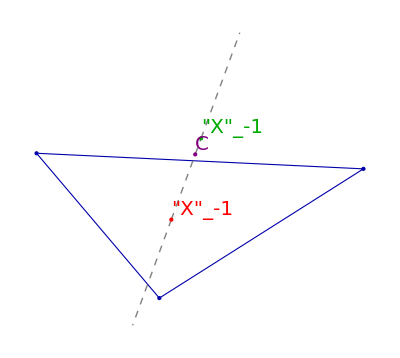

```mathematica
getInstEnv[1.5,getIncenterTrilin,getCircumcenterTrilin,instEnvDeg->10.,fntSize->20,clr12->Directive[Dashed,Gray]]
```

```mathematica
Clear@getEnvelopeObjs;
Options@getEnvelopeObjs=Join[Options@getInstEnv,{perfGoal->"Quality",slack->.05,envDashed->False,drEnv->True,drEvolute->False,drFoci->False,trilinFn3->None,omitLocus1->False,omitLocus2->False,clr3->Orange,drEllAxes->True,clrEll->Black,fillEnv->False,clrEnvFill->{Opacity@.5,Purple},fillEnvDegStep->.1,batEll->False,batEllFill->Darker@Yellow,batEllFactor->1.1}];
getEnvelopeObjs[a_,trilfn1_,trilfn2_,opts:OptionsPattern[]]:=Module[{ell,ons,x1pp,x2pp,envpp,evolute,foci,x3pp,pr,envppFill,envppTab,envMaxY,envMaxX,instEnv},
ell=If[OptionValue@drEllAxes,plotEllAxes[a,{OptionValue@clrEll,Thick}],plotEll[a,{OptionValue@clrEll,Thick}]];
pr={{-a-OptionValue@slack,a+OptionValue@slack},{-1-OptionValue@slack,1+OptionValue@slack}};
x1pp=If[OptionValue@omitLocus1,{},Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg+OptionValue@eps];trilfn1[ons[[1]],ons[[3]]],{tDeg,0,180},
PerformanceGoal->OptionValue@perfGoal,Exclusions->{Automatic,Cos[toRad@tDeg]==0,Sin[toRad@tDeg]==0},
PlotStyle->Directive[Thick,OptionValue@clr1],PlotRange->pr]];
x3pp=If[(OptionValue@trilinFn3)===None,{},
Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg+OptionValue@eps];(OptionValue@trilinFn3)[ons[[1]],ons[[3]]],{tDeg,0,180},
PerformanceGoal->OptionValue@perfGoal,Exclusions->{Automatic,Cos[toRad@tDeg]==0,Sin[toRad@tDeg]==0},
PlotStyle->Directive[Thick,OptionValue@clr3],PlotRange->pr]];
x2pp=If[OptionValue@omitLocus2,{},Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg+OptionValue@eps];
trilfn2[ons[[1]],ons[[3]]],{tDeg,0,180},
PerformanceGoal->OptionValue@perfGoal,Exclusions->{Automatic,Cos[toRad@tDeg]==0,Sin[toRad@tDeg]==0},PlotStyle->Directive[Thick,OptionValue@clr2],PlotRange->pr]];
envppTab=If[OptionValue@fillEnv,Table[getEnvelope[a,tDeg+OptionValue@eps,trilfn1,trilfn2],{tDeg,-180,180,OptionValue@fillEnvDegStep}],{}];
envMaxX=If[OptionValue@fillEnv,Max[First/@envppTab],0];
envMaxY=If[OptionValue@fillEnv,Max[Second/@envppTab],0];
envppFill=Graphics@If[OptionValue@fillEnv,{
If[OptionValue@batEll,{OptionValue@batEllFill,Disk[{0,0},OptionValue@batEllFactor{envMaxX,envMaxY}]},{}],
{EdgeForm@None,FaceForm[OptionValue@clrEnvFill],Polygon@envppTab}
},{}];
envpp=If[OptionValue@drEnv,Quiet@ParametricPlot[getEnvelope[a,tDeg,trilfn1,trilfn2],
{tDeg,0,180},PerformanceGoal->OptionValue@perfGoal,PlotStyle->If[OptionValue@envDashed,Directive[Thick,Dashed,OptionValue@clrEnv],
Directive[Thick,OptionValue@clrEnv]],PlotRange->pr],{}];
instEnv=getInstEnv[a,trilfn1,trilfn2,FilterRules[{opts},Options@getInstEnv]];
evolute=If[OptionValue@drEvolute,ellEvolute[a,1,FilterRules[{opts},Options@ellEvolute]],{}];
foci=Graphics[{PointSize@Large,Black,Point[getFoci[a]]}];
<|
"envppFill"->envppFill,
"ell"->ell,
"x1pp"-> x1pp,
"x2pp"-> x2pp,
"x3pp"->x3pp,
"ellEvolute"->evolute,
"envpp"->envpp,
"instEnv"->instEnv,
"foci"->foci
|>];
```

```mathematica
Clear@showEnvelopePairLow;
Options@showEnvelopePairLow=Join[{imgSize->800,drCirc->False,"n3"->-1,adigs->3},Options@getEnvelopeObjs];
showEnvelopePairLow[a_,trilsFn1_,trilsFn2_,opts:OptionsPattern[]]:=Module[{envL,envT,circ,eps=.0001,magn2s,pl,pr},
envL=getEnvelope[a,eps,trilsFn1,trilsFn2];envT=getEnvelope[a,90+eps,trilsFn1,trilsFn2];
magn2s=magn2/@{envL,envT};
circ=Graphics[If[OptionValue@drCirc,
{Dashed,Thick,Blue,Circle[{0,0},Max[magn/@{envL,envT}]]},{}]];
pr={{-a-OptionValue@slack,a+OptionValue@slack},{-1-OptionValue@slack,1+OptionValue@slack}};
pl="a/b="<>nfn[a,OptionValue@adigs]<>" ["<>subscriptTxtClr["X",OptionValue@"n1",OptionValue@clr1]<>","<>subscriptTxtClr["X",OptionValue@"n2",OptionValue@clr2]<>If[OptionValue@"n3"≠-1,","<>subscriptTxtClr["X",OptionValue@"n3",OptionValue@clr3],""]<>"]"<>If[negl@Abs[magn2s[[1]]-magn2s[[2]]],"*",""];
(*ctr1=newCentersFromFile[[n1]];ctr2=newCentersFromFile[[n2]];*)
Show[Append[List@@getEnvelopeObjs[a,trilsFn1,trilsFn2,FilterRules[{opts},Options@getEnvelopeObjs]],circ],
Axes->None,ImageSize->OptionValue@imgSize,PlotRange->pr,
PlotLabel->Style[pl,20]]];
```

```mathematica
Clear@showEnvelopePair;
Options@showEnvelopePair=Options@showEnvelopePairLow;
showEnvelopePair[a_,opts:OptionsPattern[]]:=Module[{trilsFn1,trilsFn2},
trilsFn1=getNewCenters[#1,#2,{OptionValue@n1}][[1,3]]&;
trilsFn2=getNewCenters[#1,#2,{OptionValue@n2}][[1,3]]&;
showEnvelopePairLow[a,trilsFn1,trilsFn2,FilterRules[{opts},Options@showEnvelopePairLow]]];
```

```mathematica
Clear@exportEnvelopeEvolutePair;exportEnvelopeEvolutePair[a_,n1_,n2_]:=Module[{fname,env},
fname="pics_env_evolute/envEvolute_"<>padZ[n1,3]<>"_"<>padZ[n2,3]<>".png";
(* showEnvelopePair[a,"n1"->1,"n2"->5,perfGoal->"Speed",drCirc->False,drEvolute->True,drFoci->True,imgSize->400] *)
env=showEnvelopePair[a,"n1"->n1,"n2"->n2,perfGoal->"Quality",slack->.3,drCirc->False,drEvolute->True,imgSize->800];
Export[fname,env]];
```

#### Export Envelope Tuples (non-collinear with X9) to file

```mathematica
Clear@exportEnvelopePair;
Options@exportEnvelopePair={extension->".png",dir->"pics_env"};
exportEnvelopePair[a_,n1_,n2_,OptionsPattern[]]:=Module[{fname,env},
fname=OptionValue@dir<>"/env_"<>padZ[n1,3]<>"_"<>padZ[n2,3]<>OptionValue@extension;
(* showEnvelopePair[a,"n1"->1,"n2"->5,perfGoal->"Speed",drCirc->False,drEvolute->True,drFoci->True,imgSize->400] *)
env=showEnvelopePair[a,"n1"->n1,"n2"->n2,slack->.2,drCirc->False,drEvolute->True];
Export[fname,env]];
```

#### Centers are collinear when their trilinears have zero determinant

```mathematica
Clear@collinearCentersLow;
collinearCentersLow[n1_,n2_,n3_]:=FullSimplify@Det[Second/@newCentersFromFile[[{n1,n2,n3}]]]
```

```mathematica
Clear@collinearCenters;
collinearCenters[n1_,n2_,n3_]:=collinearCentersLow[n1,n2,n3]===0
```

```mathematica
collinear3[ps_]:=Det[Append[#,1.]&/@ps];
```

#### This numeric solution (dependent on a) simply reports if the sum of determinants is neglible

```mathematica
collinearCentersNum[a_,n1_,n2_,n3_]:=Module[{eps=.001,n=11,ts,onss,ctrss,dets},
ts=Range[0,π,π/n]+.001;
onss=orbitNormals[a,#]&/@ts;
ctrss=(Third/@getNewCenters[#[[1]],#[[3]],{n1,n2,n3}])&/@onss;
dets=collinear3/@ctrss;
negl[Total[Abs/@dets]]]
```

```mathematica
collinearCentersNum[1.5,9,11,4]
```

False

## Evolutes and Envelopes

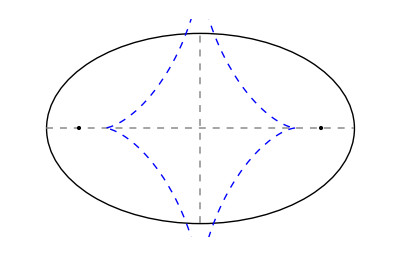

```mathematica
ellEvolute[1.618,1,slack->.1]
```

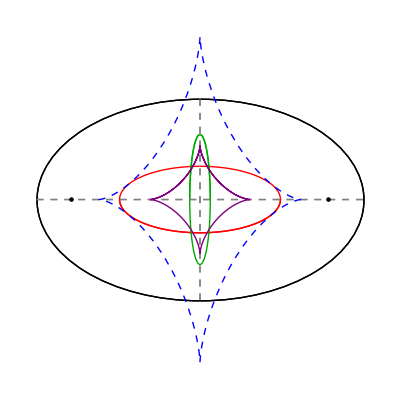

```mathematica
Show[List@@getEnvelopeObjs[1.618,getIncenterTrilin,getCircumcenterTrilin,drEvolute->True]]
```

#### X162 and X88, both on billiard, uneventful

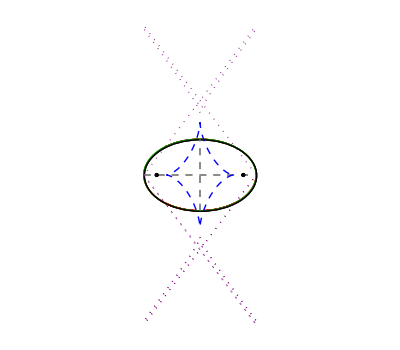

```mathematica
Module[{a=1.57,slack=3},Show[List@@getEnvelopeObjs[a,getX162Trilin,getX88Trilin,envDashed->True,drEnv->True,drFoci->True,drEvolute->True],PlotRange->{{-a-slack,a+slack},{-1-slack,1+slack}}]]
```

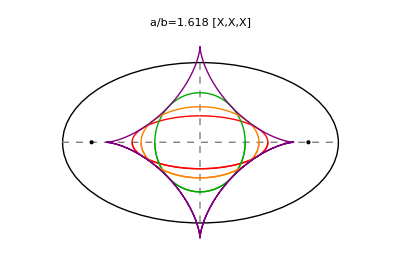

```mathematica
tripleTangPlot=showEnvelopePairLow[1.618,getIncenterTrilin,getNinepointCenterTrilin,"n1"->1,"n2"->5,"n3"->12,trilinFn3->getX12Trilin,drEvolute->False,slack->.3,imgSize->400]
```

```mathematica
export4["1190_triple_tang",tripleTangPlot]
```

```mathematica
Module[{a=1.618,pairs,envs},
pairs={
{1,5},{1,11},{1,14},{1,17},
{1,41},{1,60},{1,61},(*{1,68},*)
{1,80},{1,83},{1,85},{1,88},
(*{1,90},*)(*{1,91},*){1,94},{1,98},
{1,99},{1,100}};
envs=showEnvelopePair[a,"n1"->#[[1]],"n2"->#[[2]],perfGoal->"Speed",slack->.3,drCirc->False,drEvolute->True,imgSize->400]&/@pairs;
Grid[Partition[Append[envs,SpanFromLeft],4],Spacings->{0,0},Alignment->Left]]
```

$Aborted

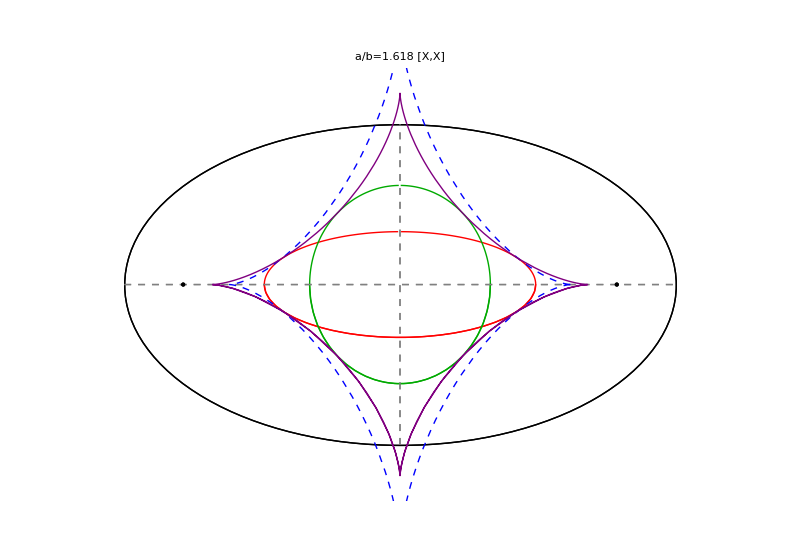

```mathematica
evolutex1x5Plot=showEnvelopePair[1.618,"n1"->1,"n2"->5,perfGoal->"Speed",slack->.3,drCirc->False,drEvolute->True,imgSize->800]
```

```mathematica
export4["1190_x1_x5_evolute",evolutex1x5Plot]
```

```mathematica
(*exportEnvelopeEvolutePair[1.618,#[[1]],#[[2]]]&/@{{1,5},{1,11},{1,14},{1,17},
{1,41},{1,60},{1,61},(*{1,68},*)
{1,80},{1,83},{1,85},{1,88},
(*{1,90},*)(*{1,91},*){1,94},{1,98},
{1,99},{1,100}};*)
```

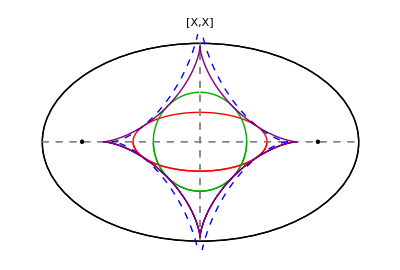
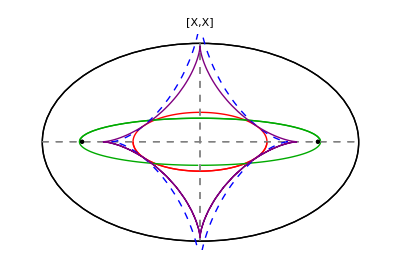
Grid[{-Graphics-,-Graphics-}]

```mathematica
Module[{a=1.5},
Grid[{showEnvelopePair[a,"n1"->1,"n2"->5,perfGoal->"Speed",drCirc->False,drEvolute->True,drFoci->True,imgSize->400],
showEnvelopePair[a,"n1"->1,"n2"->11,perfGoal->"Speed",drCirc->False,drEvolute->True,drFoci->True,imgSize->400]}]]
```

#### It seems X_34 passes through foci above a certain a/b threshold.

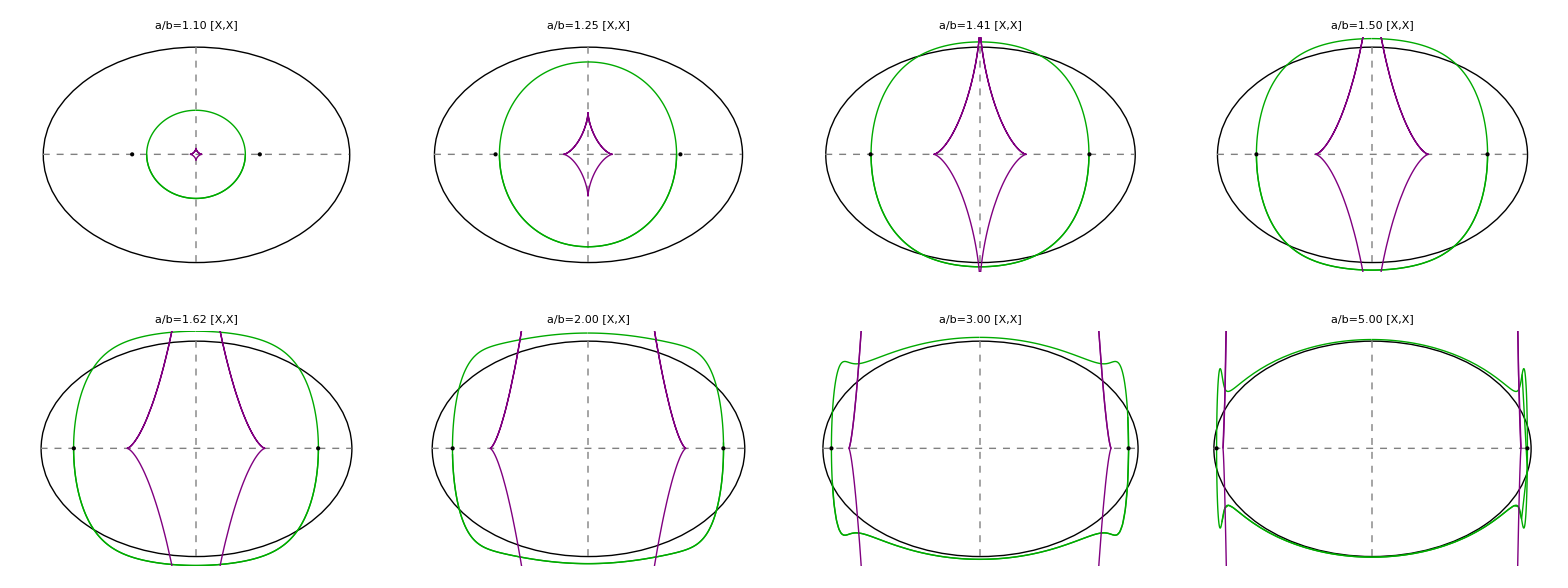

```mathematica
Grid[showEnvelopePair[#,"n1"->1,"n2"->34,perfGoal->"Quality",slack->.05,drCirc->False,imgSize->400,omitLocus1->True]&/@{1.1,1.25,1.41421,1.5,1.618,2,3,5}//Partition[#,4]&]
```

#### Euler Line (X2, X3), (X3,X4)

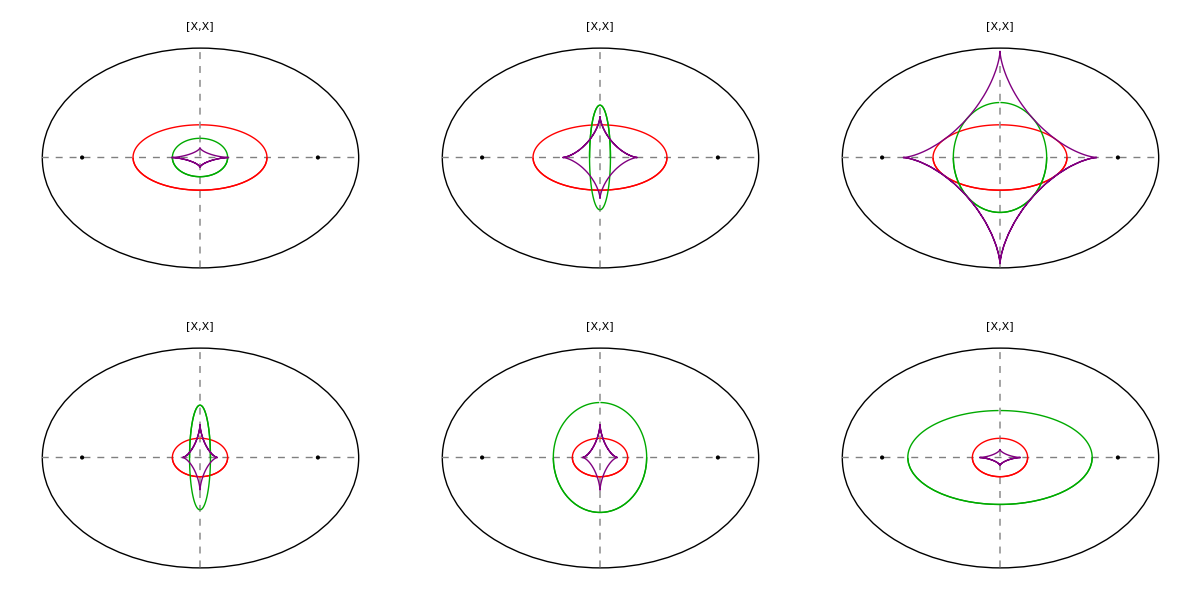

```mathematica
eulerEnvPlot=Module[{a=1.5,pairs,envs},
pairs={
{1,2},{1,3},{1,5},
{2,3},{2,5},{2,6}};
envs=showEnvelopePair[a,"n1"->#[[1]],"n2"->#[[2]],perfGoal->"Speed",slack->.05,drCirc->False,imgSize->400]&/@pairs;
Grid[Partition[envs,3]]]
```

```mathematica
export4["1200_euler_envelope_pairs",eulerEnvPlot]
```

#### Exports some 638 frames, slow

```mathematica
doEnvCtrs=False;
If[doEnvCtrs,
Module[{a=.5(Sqrt[5]+1),fname,ctrs,tups,tupsNC,tupsRestr},
(*DeleteFile[FileNames["pics_env/*.png"]];*)
(* do not include mitten nor euler inf point *)
ctrs=Delete[Range[100],{{9},{30}}];
tups=Subsets[ctrs,{2}];
Print["Original tuples: ",Length@tups];
tupsNC=Select[tups,Not[collinearCentersNum[a,9,#[[1]],#[[2]]]]&];
Print["Non-collinear tups: ",Length@tupsNC];
tupsRestr=Select[tupsNC,MemberQ[{1,2,3,4,5,6,11},#[[1]]]&];
Print["tups X(i) with i=1,2,3,4,5,6,11: ",Length@tupsRestr];
exportEnvelopePair[a,#[[1]],#[[2]]]&/@tupsRestr
]; 
]
```

#### Export Selected Frames for envelopes1618.Rmd website (R/github)

```mathematica
CreateDirectory["pics_env"]
```

CreateDirectory::filex: "C:\\Users\\drezn\\Dropbox\\Mathematica\\Billiards\\pics_env\\" already exists.

C:\Users\drezn\Dropbox\Mathematica\Billiards\pics_env

```mathematica
doEnvelopePics=False;
If[doEnvelopePics,Module[{a=.5(Sqrt[5]+1),fname,tupsTaxonomy,tupsBestOf,tups},
(*DeleteFile[FileNames["pics_env/*.png"]];*)
(* do not include mitten nor euler inf point *)
tupsTaxonomy={
(*No tangency*){1,3},{1,7},{1,13},{2,3},{2,4},{2,5},{3,4},{3,5},{3,6},{4,5},{4,8},{4,12},
(*Single tangency*){1,11},{1,14},{1,48},{2,11},{2,14},{2,35},{3,11},{3,14},{3,48},{4,14},{5,11},
(*Dual tangency*){1,5},{1,12},{1,17},{3,8},{4,32},{5,6},{5,12},{5,17},{11,48}
};
tupsBestOf={
(*Heart-Shaped*){47,52},{24,59},{36,50},
(*"Spikeys",*){26,53},{94,100},{5,53},{53,59},{40,92},
(*X(92) Batman*){5,92},{23,92},{31,92},{62,92},
(*Quasi-Diamond*){31,65},{54,83},
(*Close-Tracking*){4,59},{36,59},{49,60},{99,100},
(*Multiple Tangents*){23,59},{88,90},{51,92},
(*Misc*){49,91},{69,99},
(*X(96) Brazil Flag*) {2,96},{37,96}
};
tups=Join[tupsTaxonomy,tupsBestOf];
Print["Envelopes: ",Length@tupsBestOf];
(Print@#;exportEnvelopePair[a,#[[1]],#[[2]]])&/@tupsBestOf
]];
```

## Envelope of Pairs of Boundary Swans (Moses Points)

#### Note : mosesIsotomicsTrils must be initialized! (see orbits_v5.nb)

```mathematica
Clear@mosesIsotomicsTrils;
mosesIsotomicsTrils=Get["mosesIsotTrils.m"];
```

```mathematica
Part[#,{1,2,5,6}]&/@mosesIsotomicsTrils//Take[#,10]&//TableForm
```

index | center | isotomic | in pm list
1 | 514 | 190 | True
2 | 661 | 799 | True
3 | 693 | 100 | True
4 | 857 | Null | False
5 | 908 | 34234 | True
6 | 914 | Null | False
7 | 1577 | 662 | True
8 | 1959 | 1821 | True
9 | 2084 | Null | False

```mathematica
Clear@showEnvelopeSwanPair;
Options@showEnvelopeSwanPair=Options@showEnvelopePairLow;
(* isotN1 and isotN2 are in 1 to Length@mosesIsotomicsTrils-1 *)
showEnvelopeSwanPair[a_,isotN1_,isotN2_,opts:OptionsPattern[]]:=Module[{trilsFn1,trilsFn2,ctrN1,ctrN2,ellN1,ellN2},
trilsFn1=getOneMosesIsotomicTrilin[#1,#2,isotN1]&;
trilsFn2=getOneMosesIsotomicTrilin[#1,#2,isotN2]&;
(* these are on L55 *)
ctrN1=mosesIsotomicsTrils[[isotN1+1,2]];
ctrN2=mosesIsotomicsTrils[[isotN2+1,2]];
(* their isotomic conjugates on E9 *)
(* if X(k) for the ellipse does not exist use -k, where k is the point lying on L55 *)
ellN1=mosesIsotomicsTrils[[isotN1+1,5]];If[!NumberQ@ellN1,ellN1=-ctrN1];
ellN2=mosesIsotomicsTrils[[isotN2+1,5]];If[!NumberQ@ellN2,ellN2=-ctrN2];
showEnvelopePairLow[a,
trilsFn1,(* takes orbit and sides *)
trilsFn2,
FilterRules[{opts,n1->ellN1,n2->ellN2},Options@showEnvelopePairLow]]];
```

```mathematica
Clear@exportEnvelopeSwanPair;
Options@exportEnvelopeSwanPair={extension->".png",dir->"pics_env",slackX->1,slackY->1};
exportEnvelopeSwanPair[a_,n1_,n2_,OptionsPattern[]]:=Module[{fname,env,pr},
fname=OptionValue@dir<>"/env_"<>padZ[n1,3]<>"_"<>padZ[n2,3]<>OptionValue@extension;
(* showEnvelopePair[a,"n1"->1,"n2"->5,perfGoal->"Speed",drCirc->False,drEvolute->True,drFoci->True,imgSize->400] *)
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
env=Show[showEnvelopeSwanPair[a,n1,n2,perfGoal->"Quality",omitLocus1->True,omitLocus2->True],PlotRange->pr,ImageSize->800];
Export[fname,env]];
```

```mathematica
(*exportEnvelopeSwanPair[1.5,1,2,dir->"pics_env_swan"]*)
```

#### X799 and pX662 are isotomic/isogonal conjugates of the same X661

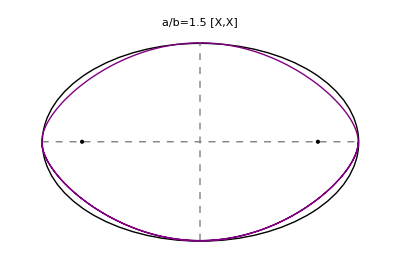

```mathematica
Show[showEnvelopeSwanPair[1.5,2,7,perfGoal->"Quality",omitLocus1->True,omitLocus2->True,slackY->1,adigs->1],ImageSize->400]
```

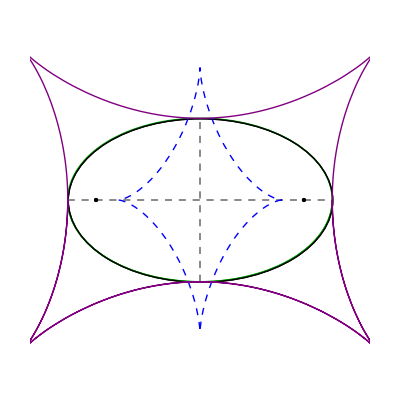

```mathematica
Show[List@@getEnvelopeObjs[1.618,getX661Trilin,getX662Trilin,drEvolute->True],PlotRange->{{-2,2},{-2,2}}]
```

#### X190 e X799 sao muuuuuito proximos do bilhar!

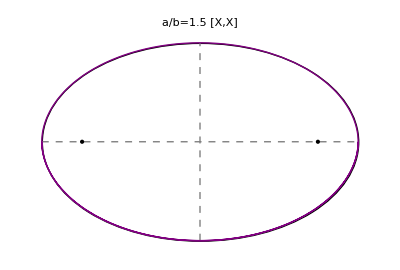

```mathematica
Show[showEnvelopeSwanPair[1.5,1,2,perfGoal->"Quality",omitLocus1->True,omitLocus2->True,slackY->1,adigs->1],ImageSize->400]
```

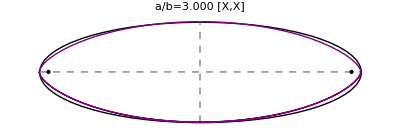

```mathematica
Show[showEnvelopeSwanPair[3,1,3,perfGoal->"Quality",omitLocus1->True,omitLocus2->True],ImageSize->400]
```

```mathematica
doEnvSwanPairs=False;
If[doEnvSwanPairs,
Module[{a=.5(Sqrt[5]+1),fname,ctrs,tups,tupsNC,tupsRestr},
(*DeleteFile[FileNames["pics_env/*.png"]];*)
(* do not include mitten nor euler inf point *)
ctrs=Range[Length@mosesIsotomicsTrils-1];
tups=Subsets[ctrs,{2}];
Print["Original tuples: ",Length@tups];
tupsRestr=Select[tups,!MemberQ[{1,2},#[[1]]]&];
Print["tups X(i) with i~=1,2: ",Length@tupsRestr];
exportEnvelopeSwanPair[a,#[[1]],#[[2]],dir->"pics_env_swan"]&/@tupsRestr
]
];
```

## Envelope of Center and Swan Pair

```mathematica
Options@showEnvelopePairLow
```

{imgSize→800,drCirc→False,n3→-1,adigs→3,eps→0.001,instEnvDeg→None,envRayL→3,n1→-1,n2→-1,clr1→-Graphics-,clr2→-Graphics-,clrEnv→-Graphics-,txtLgt→1.25,fntSize→16,perfGoal→Quality,slack→0.05,envDashed→False,drEnv→True,drEvolute→False,drFoci→False,trilinFn3→None,omitLocus1→False,omitLocus2→False,clr3→-Graphics-,drEllAxes→True,clrEll→-Graphics-,fillEnv→False,clrEnvFill→{Opacity[0.5],-Graphics-},fillEnvDegStep→0.1,batEll→False,batEllFill→-Graphics-,batEllFactor→1.1}

```mathematica
Print[mosesIsotomicsTrils[[54,5]]]
```

Null

```mathematica
Clear@showEnvelopeCenterSwan;
Options@showEnvelopeCenterSwan=Options@showEnvelopePairLow;
(* isotN are in 1 to Length@mosesIsotomicsTrils-1 *)
showEnvelopeCenterSwan[a_,n_,isotN_,opts:OptionsPattern[]]:=Module[{trilsCtrFn,trilsSwanFn,ctrN,ellN},
trilsCtrFn=getNewCenters[#1,#2,{n}][[1,3]]&;
trilsSwanFn=getOneMosesIsotomicTrilin[#1,#2,isotN]&;
(* their isotomic conjugates on E9 *)
(* if X(k) for the ellipse does not exist use -k, where k is the point lying on L55 *)
ellN=mosesIsotomicsTrils[[isotN+1,5]];If[!NumberQ@ellN,ellN=-mosesIsotomicsTrils[[isotN+1,2]]];
showEnvelopePairLow[a,
trilsCtrFn,(* takes orbit and sides *)
trilsSwanFn,
FilterRules[{n1->n,n2->ellN,opts},Options@showEnvelopePairLow]]];
```

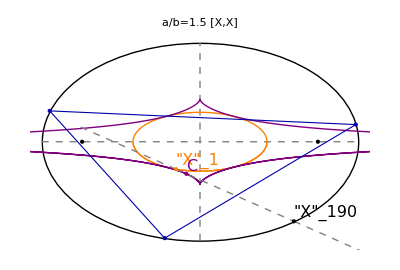

```mathematica
showEnvelopeCenterSwan[1.5,1,1,omitLocus2->True,clr1->Orange,clr2->Black,instEnvDeg->10.,imgSize->400,adigs->1,clr12->Directive[Dashed,Gray]]
```

```mathematica
Clear@exportEnvelopeCenterSwan;
Options@exportEnvelopeCenterSwan={extension->".png",dir->"pics_env_center_swan",slackX->1,slackY->1};
exportEnvelopeCenterSwan[a_,centerN_,swanN_,OptionsPattern[]]:=Module[{fname,env,pr},
fname=OptionValue@dir<>"/env_"<>padZ[centerN,3]<>"_"<>padZ[swanN,3]<>OptionValue@extension;
(* showEnvelopePair[a,"n1"->1,"n2"->5,perfGoal->"Speed",drCirc->False,drEvolute->True,drFoci->True,imgSize->400] *)
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
env=Show[showEnvelopeCenterSwan[a,centerN,swanN,omitLocus2->True,clr1->Darker@Green,clr2->Black,perfGoal->"Quality"],PlotRange->pr,ImageSize->800];
Export[fname,env]];
```

```mathematica
exportEnvelopeCenterSwan[1.5,1,2]
```

pics_env_center_swan/env_0001_0002.png

```mathematica
doEnvCenterSwanPairs=False;
If[doEnvCenterSwanPairs,
Module[{a=.5(Sqrt[5]+1),fname,ctrs,ctrsIsot,tups,tupsNC,tupsRestr},
ctrs=Delete[Range[100],{{9},{30},{88},{100}}];
ctrsIsot=Range[Length@mosesIsotomicsTrils-1]; 
tups=Tuples[{ctrsIsot,ctrs}];
Print["Original tuples: ",Length@tups];
tupsRestr=tups (*Select[tups,MemberQ[{1,2},#[[1]]]&]*);
Print["tups selected: ",Length@tupsRestr];
exportEnvelopeCenterSwan[a,#[[2]],#[[1]]]&/@tupsRestr
]; 
]
```

## Batman Video

-Graphics-

```mathematica
Select[Part[#,{1,2,3}]&/@mosesIsotomicsTrils,#[[1]]=="index"||#[[2]]==30565&]//TableForm
```

index | center | description
53 | 30565 | CENTROID OF SIDE-TRIANGLE OF GEMINI TRIANGLES 2 AND 30

```mathematica
Options@showEnvelopeCenterSwan
```

{eps→0.001,imgSize→800,drCirc→False,n3→-1,adigs→3,eps→0.001,instEnvDeg→None,envRayL→3,n1→-1,n2→-1,clr1→-Graphics-,clr2→-Graphics-,clrEnv→-Graphics-,txtLgt→1.25,perfGoal→Quality,slack→0.05,envDashed→False,drEnv→True,drEvolute→False,drFoci→False,trilinFn3→None,omitLocus1→False,omitLocus2→False,clr3→-Graphics-,drEllAxes→True,clrEll→-Graphics-,fillEnv→False,clrEnvFill→{Opacity[0.5],-Graphics-},fillEnvDegStep→0.1,batEll→False,batEllFill→-Graphics-,batEllFactor→1.1}

```mathematica
Clear@showBatmanLowEnvOnly;
Options@showBatmanLowEnvOnly=Join[Options@showEnvelopeCenterSwan,{(*slackX->.5,slackY->.2*)(*,n1->48,n2->53*),backgr->Black,clrLab->Gray,backgrLeg->White,amax->-1,doLegend->False}];
showBatmanLowEnvOnly[a_,opts:OptionsPattern[]]:=Module[{env,rules},
rules=FilterRules[{opts},Options@showEnvelopeCenterSwan];
(* expensive, can it be passed? *)
env=showEnvelopeCenterSwan[a,OptionValue@n1,OptionValue@n2,rules];
env];
```

```mathematica
Clear@showBatmanLowFast;
Options@showBatmanLowFast=Join[Options@showEnvelopeCenterSwan,{slackX->.5,slackY->.2(*,n1->48,n2->53*),backgr->Black,clrLab->Gray,rotAng->90.,backgrLeg->White,amax->-1,doLegend->False}];
showBatmanLowFast[a_,env_,opts:OptionsPattern[]]:=Module[{prRot,envRot,trilsCtrFn,trilsSwanFn,instEnv,rules,pl,isot,ar,theShow,ellN},
ar=If[OptionValue@amax>0,OptionValue@amax,a];
prRot={{-1-OptionValue@slackX,1+OptionValue@slackX},{-ar-OptionValue@slackY,ar+OptionValue@slackY}};
rules=FilterRules[{opts},Options@showEnvelopeCenterSwan];
(* expensive, can it be passed? *)
(*env=showEnvelopeCenterSwan[a,OptionValue@n1,OptionValue@n2,rules];*)
(* needs to stencil the position *)
trilsCtrFn=getNewCenters[#1,#2,{OptionValue@n1}][[1,3]]&;
trilsSwanFn=getOneMosesIsotomicTrilin[#1,#2,OptionValue@n2]&;
ellN=mosesIsotomicsTrils[[OptionValue@n2+1,5]];
If[!NumberQ@ellN,ellN=-mosesIsotomicsTrils[[OptionValue@n2+1,2]]];
instEnv=getInstEnv[a,trilsCtrFn,trilsSwanFn,FilterRules[{n2->ellN,opts},Options@getInstEnv]];
envRot=Graphics[{Rotate[Join[List@@env,List@@instEnv],
toRad[OptionValue@rotAng],{0,0}],{Text[Style["(c) 2020 Dan Reznik",{Darker@Gray,16}],{1+OptionValue@slackX,-ar-OptionValue@slackY},{1.25,-1},Background->OptionValue@backgr]}}];
pl="a/b="<>nfn[a,OptionValue@adigs];
isot="isot["<>ToString[Subscript["X",mosesIsotomicsTrils[[OptionValue@n2+1,2]]],StandardForm]<>"]";
theShow=Show[{envRot},Background->OptionValue@backgr,PlotRange->prRot,PlotLabel->Style[pl,{OptionValue@clrLab,16}],ImageSize->OptionValue@imgSize];
If[OptionValue,doLegend,Legended[theShow,
Placed[LineLegend[Directive[AbsoluteThickness[3],#]&/@{OptionValue@clr1,OptionValue@clrEll},Style[#,{Black,16}]&/@{ToString[Subscript["X",OptionValue@n1],StandardForm],isot},LegendLayout->"Row"(*,LegendBackground->OptionValue@backgrLeg*)],Below]],theShow]];
```

```mathematica
@
```

```mathematica
Options@showBatmanLowFast
```

{imgSize→800,drCirc→False,n3→-1,adigs→3,eps→0.001,instEnvDeg→None,envRayL→1,n1→-1,n2→-1,clr1→-Graphics-,clr2→-Graphics-,clrEnv→-Graphics-,txtLgt→1.25,fntSize→16,clr12→-Graphics-,perfGoal→Quality,slack→0.05,envDashed→False,drEnv→True,drEvolute→False,drFoci→False,trilinFn3→None,omitLocus1→False,omitLocus2→False,clr3→-Graphics-,drEllAxes→True,clrEll→-Graphics-,fillEnv→False,clrEnvFill→{Opacity[0.5],-Graphics-},fillEnvDegStep→0.1,batEll→False,batEllFill→-Graphics-,batEllFactor→1.1,slackX→0.5,slackY→0.2,backgr→-Graphics-,clrLab→-Graphics-,rotAng→90.,backgrLeg→-Graphics-,amax→-1,doLegend→False}

```mathematica
Clear@showBatmanLow;
(*Options@showBatmanLow=Join[Options@showEnvelopeCenterSwan,{slackX->.5,slackY->.2(*,n1->48,n2->53*),backgr->Black,clrLab->Gray,rotAng->90.,backgrLeg->White,amax->-1,doLegend->False}];
showBatmanLow[a_,opts:OptionsPattern[]]:=Module[{prRot,env,envRot,rules,pl,isot,ar,theShow},
ar=If[OptionValue@amax>0,OptionValue@amax,a];
prRot={{-1-OptionValue@slackX,1+OptionValue@slackX},{-ar-OptionValue@slackY,ar+OptionValue@slackY}};
rules=FilterRules[{opts},Options@showEnvelopeCenterSwan];
(* expensive, can it be passed? *)
env=showEnvelopeCenterSwan[a,OptionValue@n1,OptionValue@n2,rules];
envRot=Graphics@Rotate[List@@env
(*Prepend[List@@env,{Darker@Yellow,Disk[{0,0},{prRot[[2,2]],prRot[[1,2]]}]}]*)
,toRad[OptionValue@rotAng],{0,0}];
pl="a/b="<>nfn[a,OptionValue@adigs];
isot="isot["<>ToString[Subscript["X",mosesIsotomicsTrils[[OptionValue@n2+1,2]]],StandardForm]<>"]";
theShow=Show[{envRot},Background->OptionValue@backgr,PlotRange->prRot,PlotLabel->Style[pl,{OptionValue@clrLab,16}],ImageSize->OptionValue@imgSize];
If[OptionValue,doLegend,Legended[theShow,
Placed[LineLegend[Directive[AbsoluteThickness[3],#]&/@{OptionValue@clr1,OptionValue@clrEll},Style[#,{Black,16}]&/@{ToString[Subscript["X",OptionValue@n1],StandardForm],isot},LegendLayout->"Row"(*,LegendBackground->OptionValue@backgrLeg*)],Below]],theShow]];*)
```

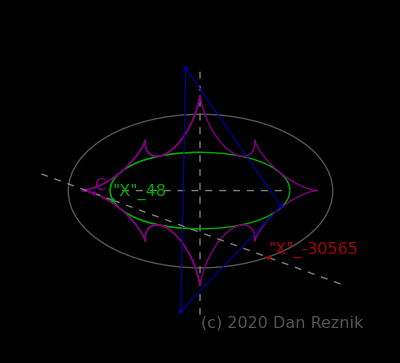

```mathematica
Module[{a=1.618,env},
env=showBatmanLowEnvOnly[a,omitLocus2->True,n1->48,n2->53,
clr1->Darker@Green,clrEnv->Purple,clrLab->Gray,drEllAxes->True,clrEll->Darker@Gray];
showBatmanLowFast[a,env,instEnvDeg->10.,n1->48,n2->53,clr1->Darker@Green,clr2->Darker@Red,clr12->Directive[Dashed,Gray],slackX->1,slackY->.2,imgSize->400]]
```

```mathematica
Clear@showBatmanPreEnv;
Options@showBatmanPreEnv=Options@showBatmanLowEnvOnly;showBatmanPreEnv[a_,opts:OptionsPattern[]]:=
showBatmanLowEnvOnly[a,n1->48,n2->53,
omitLocus2->True,
clr1->Darker@Green,clrEnv->Purple,
backgr->White,clrLab->Black,
clrLab->Gray,drEllAxes->True,clrEll->Darker@Gray,
drEllAxes->True,clrEll->Darker@Gray];
```

```mathematica
Clear@showBatmanPreFast;
Options@showBatmanPreFast=Options@showBatmanLowFast;showBatmanPreFast[a_,env_,opts:OptionsPattern[]]:=showBatmanLowFast[a,env,n1->48,n2->53,slackX->1,slackY->.2,omitLocus2->True,
clr1->Darker@Green,clr2->Darker@Red,clrEnv->Purple,clr12->Directive[Dashed,Gray],
backgr->White,clrLab->Black,
drEllAxes->True,clrEll->Darker@Gray,envRayL->1.5,FilterRules[{opts},Options@showBatmanLowFast]];
```

```mathematica
batmanPreEnv=showBatmanPreEnv[1.618];
```

```mathematica
Manipulate[
showBatmanPreFast[1.618,batmanPreEnv,instEnvDeg->tDeg,rotAng->rotAng0,imgSize->400],
{{tDeg,10.},-180,180,.1},
{{rotAng0,0.},-180,180,.1}]
```

```mathematica
Options@showBatmanLow
```

{eps→0.001,imgSize→800,drCirc→False,n3→-1,adigs→3,eps→0.001,perfGoal→Quality,slack→0.05,envDashed→False,drEnv→True,drEvolute→False,drFoci→False,trilinFn3→None,omitLocus1→False,omitLocus2→False,clr1→-Graphics-,clr2→-Graphics-,clr3→-Graphics-,drEllAxes→True,clrEll→-Graphics-,clrEnv→-Graphics-,fillEnv→False,clrEnvFill→{Opacity[0.5],-Graphics-},fillEnvDegStep→0.1,batEll→False,batEllFill→-Graphics-,batEllFactor→1.1,instEnvDeg→Null,envRayL→3,n1→-1,n2→-1,txtLgt→1.25,slackX→0.5,slackY→0.2,backgr→-Graphics-,clrLab→-Graphics-,rotAng→90.,backgrLeg→-Graphics-,amax→-1,doLegend→False}

```mathematica
Clear@showBatmanEnv;
Options@showBatmanEnv=Options@showBatmanLowEnvOnly;
showBatmanEnv[a_,opts:OptionsPattern[]]:=
showBatmanLowEnvOnly[a,n1->48,n2->53,
omitLocus2->True,
clr1->Darker@Green,clrEnv->Black,
clrEll->Darker@Gray,
clrEnvFill->{Opacity@.66,Black},fillEnv->True,fillEnvDegStep->.1,batEll->True,batEllFill->Darker@Yellow,
clrLab->Gray,drEllAxes->False,FilterRules[{opts},Options@showBatmanLowEnvOnly]];
```

```mathematica
Options@showBatmanFast=Options@showBatmanLowFast;
showBatmanFast[a_,env_,opts:OptionsPattern[]]:=showBatmanLowFast[a,env,n1->48,n2->53,
slackX->1,slackY->.2,
clr1->Darker@Green,clr2->Darker@Red,clr12->Directive[Dashed,Black],
drEllAxes->False,envRayL->1,FilterRules[{opts},Options@showBatmanLowFast]];
```

```mathematica
batmanPostEnv=showBatmanEnv[1.618];
```

```mathematica
Manipulate[
Module[{a=1.618,env},
showBatmanFast[a,batmanPostEnv,instEnvDeg->tDeg,imgSize->800,fntSize->20]],
{{tDeg,10.},-180,180,1}]
```

## Simson Envelope

#### Points on Circumcircle generate collinear Orthic -- that' s the Simson Line

circumcircle passes X_i for i = 74, 98, 99, 100, 101,
102, 103, 104, 105, 106, 107, 108, 109, 110 (focus of the Kiepert parabola), 111 (Parry point), 112,

476 (Tixier point), 477, 675, 681, 689, 691, 697, 699, 701, 703, 705, 707, 709, 711, 713, 715, 717, 719, 721, 723, 725, 727, 729, 731, 733, 735, 737, 739, 741, 743, 745, 747, 753, 755, 759, 761, 767, 769, 773, 777, 779, 781, 783, 785, 787, 789, 791, 793, 795, 797, 803, 805, 807, 809, 813, 815, 817, 819, 825, 827, 831, 833, 835, 839, 840, 841, 842, 843, 898, 901, 907, 915, 917, 919, 925, 927, 929, 930, 931, 932, 933, 934, 935, 953, 972, 1113, 1114, 1141 (Gibert point), 1286, 1287, 1288, 1289, 1290, 1291, 1292, 1293, 1294, 1295, 1296, 1297, 1298, 1299, 1300, 1301, 1302, 1303, 1304, 1305, 1306, 1307, 1308, 1309, 1310, 1311, 1379, 1380, 1381, 1382, 1477, 2222, 2249, 2291, 2365, 2366, 2367, 2368, 2369, 2370, 2371, 2372, 2373, 2374, 2375, 2376, 2377, 2378, 2379, 2380, 2381, 2382, 2383, 2384, 2687, 2688, 2689, 2690, 2691, 2692, 2693, 2694, 2695, 2696, 2697, 2698, 2699, 2700, 2701, 2702, 2703, 2704, 2705, 2706, 2707, 2708, 2709, 2710, 2711, 2712, 2713, 2714, 2715, 2716, 2717, 2718, 2719, 2720, 2721, 2722, 2723, 2724, 2725, 2726, 2727, 2728, 2729, 2730, 2731, 2732, 2733, 2734, 2735, 2736, 2737, 2738, 2739, 2740, 2741, 2742, 2743, 2744, 2745, 2746, 2747, 2748, 2749, 2750, 2751, 2752, 2753, 2754, 2755, 2756, 2757, 2758, 2759, 2760, 2761, 2762, 2763, 2764, 2765, 2766, 2767, 2768, 2769, 2770, 2855, 2856, 2857, 2858, 2859, 2860, 2861, 2862, 2863, 2864, 2865, 2866, 2867, and 2868.

Here is the list of isotomic of points on L55 to C9

```mathematica
mosesPts2={88,100,162,190,651,653,655,658,660,673,662,799,823,897,1156,1821,2349,2580,2581,3257,4598,4604,4606,4607,8052,24624,27834,32680,34234,36101};Length@mosesPts2
```

30

```mathematica
getX2TrilinRaw[{a_,b_,c_}]:={b c,c a,a b};
getX3TrilinRaw[{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}];
getX4TrilinRaw[{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
1/{(b2+c2-a2),(c2+a2-b2),(a2+b2-c2)}];
getX5TrilinRaw[{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
{b c(a2(b2+c2)-(b2-c2)^2),
c a(b2(c2+a2)-(c2-a2)^2),
a b(c2(a2+b2)-(a2-b2)^2)}];
getX6TrilinRaw[{a_,b_,c_}]:={a,b,c};
getX9TrilinRaw[{a_,b_,c_}]:={b+c-a,c+a-b,a+b-c};
getX11TrilinRaw[{a_,b_,c_}]:={
b c(b+c-a)(b-c)^2,
c a(c+a-b)(c-a)^2,
a b(a+b-c)(a-b)^2};
getX74TrilinRaw[{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c,a4,b4,c4},
a4=a2^2;b4=b2^2;c4=c2^2;
{a/(2a4-(b2-c2)^2-a2(b2+c2)),
b/(2b4-(c2-a2)^2-b2(c2+a2)),
c/(2c4-(a2-b2)^2-c2(a2+b2))}];
getX98TrilinRaw[{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c,a4,b4,c4},
a4=a2^2;b4=b2^2;c4=c2^2;
{b c/(b4+c4-a2 b2-a2 c2),
c a/(c4+a4-b2 c2-b2 a2),
a b/(a4+b4-c2 a2-c2 b2)}];
getX99TrilinRaw[{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
{b c/(b2-c2),
c a/(c2-a2),
a b/(a2-b2)}];
getX100TrilinRaw[{a_,b_,c_}]:=1/{b-c,c-a,a-b};
getX101TrilinRaw[{a_,b_,c_}]:={a/(b-c),b/(c-a),c/(a-b)};
```

```mathematica
Clear@getSimsonInfoLow;
getSimsonInfoLow[orbit_,sides_,trilsRawFn_]:=Module[{trilsRaw,p,pedal,coll},
trilsRaw=trilsRawFn@sides;
p=trilinearToCartesian[orbit,sides,trilsRaw];
(*from=closestPerp[p,ons[[1,1]],ons[[1,2]]];
to=closestPerp[p,ons[[2,1]],ons[[2,2]]];*)
pedal=pedalTriangle[orbit,sides,trilsRaw];
coll=collinear3@pedal;
If[!negl[coll],Print["pedal vertices not collinear"]];
<|"p"->p,"pedal"->pedal,"collDet"->coll,"trilsRaw"->trilsRaw|>
];
```

```mathematica
Append[<|"a"->1|>,"b"->2]
```

<|a→1,b→2|>

```mathematica
Clear@getSimsonInfo;
Options@getSimsonInfo={doExc->False};
getSimsonInfo[a_,tDeg_,trilsRawFn_,OptionsPattern[]]:=Module[{ons,info,exc,excSides},
ons=orbitNormals[a,toRad@tDeg];
If[OptionValue@doExc,
exc=excentralTriangle[ons[[1]],ons[[3]]];
excSides=triLengthsRL@exc;
Prepend[getSimsonInfoLow[exc,excSides,trilsRawFn],"ons"->{exc,exc(* wrong, filler *),excSides}],
Prepend[getSimsonInfoLow[ons[[1]],ons[[3]],trilsRawFn],"ons"->ons]]
];
```

```mathematica
Clear@getSimsonEnvelope;(* via intersection *)
Options@getSimsonEnvelope={epsDeg->.0001,doExc->False};
getSimsonEnvelope[a_?NumericQ,tDeg_?NumericQ,(* actual trilinears *)trilsRawFn_,opts:OptionsPattern[]]:=Module[{ons,si1,si2},
si1=getSimsonInfo[a,tDeg-.5OptionValue@epsDeg,trilsRawFn,FilterRules[{opts},Options@getSimsonInfo]];
si2=getSimsonInfo[a,tDeg+.5OptionValue@epsDeg,trilsRawFn,FilterRules[{opts},Options@getSimsonInfo]];
interRaysUnprot[
si1["pedal"][[1]],si1["pedal"][[2]]-si1["pedal"][[1]],
si2["pedal"][[1]],si2["pedal"][[2]]-si2["pedal"][[1]]]];
```

```mathematica
getSimsonEnvelope[1.5,10.,getX100TrilinRaw,doExc->True]
```

{-0.0358219,2.64031}

```mathematica
Clear@showSimpson;
Options@showSimpson={slackX->.2,slackY->.2,n->-1,drExc->False,drExtraTrils->False,extraTrilsRawFn->getX9TrilinRaw,imgSize->800};
showSimpson[a_,tDeg_,trilsRawFn_,env_,OptionsPattern[]]:=Module[{ons,ell,si,gr,x3,pr,pl,fs,extraTrils,extraX,extraPed,
exc,excSides,excX100,excX3,excR,excSi},
ell=plotEllAxes[a,{Thick,Black}];
fs=getFoci[a];
si=getSimsonInfo[a,tDeg,trilsRawFn];
exc=excentralTriangle[si["ons"][[1]],si["ons"][[3]]];
excSides=triLengthsRL@exc;
excX100=getX100Trilin[exc,excSides];
excX3=getCircumcenterTrilin[exc,excSides];
excR=getCircumradius@excSides;
excSi=getSimsonInfoLow[exc,excSides,trilsRawFn];
x3=getCircumcenterTrilin[si["ons"][[1]],si["ons"][[3]]];
If[OptionValue@drExtraTrils,
extraTrils=(OptionValue@extraTrilsRawFn)@si["ons"][[3]];
extraX=trilinearToCartesian[si["ons"][[1]],si["ons"][[3]],extraTrils];
extraPed=pedalTriangle[si["ons"][[1]],si["ons"][[3]],extraTrils]];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,
{PointSize@Medium,Point@{0,0},Point@fs},
{Pink,Point@x3,Dashed,Circle[x3,magn[si["ons"][[1,1]]-x3]],
Text[Style["X_3",20],x3,{-1,-1}]},
{EdgeForm@{Thick,Orange},Polygon@si["pedal"],Orange,Point@si["pedal"]},
{EdgeForm@{Thick,Blue},Polygon@si["ons"][[1]],Blue,Point@si["ons"][[1]]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@exc,Darker@Green,Point@exc,Dashed,Circle[excX3,excR],Point@excX100,Text[Style["X'_100",16],excX100,{-1,-1}],{EdgeForm@{Thick,Dashed,Orange},Polygon@excSi["pedal"],Orange,Point@excSi["pedal"]}},{}],
{Red,Point@si["p"],Text[Style[ToString[Subscript["X",OptionValue@n],StandardForm],20],si["p"],{-1,-1}]},
If[OptionValue@drExtraTrils,{EdgeForm@{Darker@Red},Polygon@extraPed,Darker@Red,Point@extraX},{}]}];
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
pl="a/b="<>nfn[a,3]<>", L_sim="<>nfn[triPer[si["pedal"]],3]<> If[OptionValue@drExtraTrils,", A_9="<>nfn[-signedArea[extraPed],2],""];
Show[{ell,env,gr},PlotRange->pr,PlotLabel->Style[pl,{Black,20}],ImageSize->OptionValue@imgSize]];
```

#### One idea : draw loci of pedal triangles with orbit vertices and/or with themselves!

```mathematica
DynamicModule[{env,excEnv},
Manipulate[
env=ParametricPlot[getSimsonEnvelope[a,tDeg2,getX100TrilinRaw],{tDeg2,0,180},PlotStyle->{Thick,Purple},PerformanceGoal->"Quality"];
excEnv=ParametricPlot[getSimsonEnvelope[a,tDeg2,getX100TrilinRaw,doExc->True],{tDeg2,0,180},PlotStyle->{Thick,Dashed,Purple},PerformanceGoal->"Quality"];
Dynamic@showSimpson[a,tDeg,getX100TrilinRaw,{env,excEnv},n->100,slackX->3,slackY->3,drExc->drExc0],
{{a,1.5},1.1,3,.05},
{{tDeg,10.},-180,180,.1},
{{drExc0,False},{True,False}},SaveDefinitions->True]
]
```

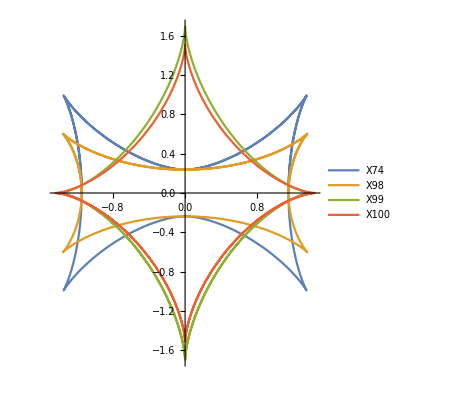

```mathematica
ParametricPlot[
{getSimsonEnvelope[1.5,tDeg,getX74TrilinRaw],
getSimsonEnvelope[1.5,tDeg,getX98TrilinRaw],
getSimsonEnvelope[1.5,tDeg,getX99TrilinRaw],
getSimsonEnvelope[1.5,tDeg,getX100TrilinRaw]}
,{tDeg,0,180},PlotLegends->{"X74","X98","X99","X100"}]
```

## Envelope X88 with collinear X1 and X100

```mathematica
Clear@showX88complexLow;
Options@showX88complexLow={slackX->1,slackY->.2,size->800};
showX88complexLow[a_,tDeg_,objs_,OptionsPattern[]]:=Module[{ons,gr,ps,eps=.001,env,a1,b1},
ell=plotEllAxes[a,{Black,Thick}];
(*x1pp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg1+eps];getIncenterTrilin[ons[[1]],ons[[3]]],{tDeg1,0,180},PerformanceGoal->"Speed",PlotStyle->Directive[Darker@Green,Thick]];
envpp=Quiet@ParametricPlot[getEnvelope[a,tDeg1,getIncenterTrilin,getX100Trilin],
{tDeg1,0,180},PerformanceGoal->"Speed",PlotStyle->Directive[Thick,Lighter@Purple]];*)
ons=orbitNormals[a,toRad@tDeg];
env=getEnvelope[a,tDeg,getIncenterTrilin,getX100Trilin];
ps=#[ons[[1]],ons[[3]]]&/@{getIncenterTrilin,getX100Trilin,getX88Trilin};
{a1,b1}=getIncenterAxes[a];
gr=Graphics[{FaceForm@None,Thick,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]]},
{Dashed,Line@{Second@ps,Last@ps}},
{Purple,Point@env,Text[Style["E",20],env,{-1.25,-1.25}]},
{Red,Point@ps,
(* ellLabelTxtb[a_,b_,p_,txt_,lgt_,opts:OptionsPattern[]] *)
MapThread[ellLabelTxtb[#1,#2,#3,Style[Subscript["X",#4],20],.125]&,
{{a1,a,a},{b1,1,1},ps,{1,100,88}}](*,
MapThread[Text[Style[Subscript["X",#1],20],#2,{1.,1.25}]&,{{1,100,88},ps}]*)}}];
Show[{objs[["ell"]],objs[["x1pp"]],objs[["envpp"]],gr},ImageSize->OptionValue@size,PlotLabel->Style["a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°",20],PlotRange->{{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}}]];
```

```mathematica
Clear@showX88complexObjs;
showX88complexObjs[a_]:=Module[{ons,gr,ell,ps,x1pp,eps=.001,envelope,x1a,x1b,x100a,x100b,envpp,env},
ell=plotEllAxes[a,{Black,Thick}];
x1pp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg1+eps];getIncenterTrilin[ons[[1]],ons[[3]]],{tDeg1,0,180},PerformanceGoal->"Speed",PlotStyle->Directive[Darker@Green,Thick]];
envpp=Quiet@ParametricPlot[getEnvelope[a,tDeg1,getIncenterTrilin,getX100Trilin],
{tDeg1,0,180},PerformanceGoal->"Speed",PlotStyle->Directive[Thick,Lighter@Purple]];
<|"x1pp"-> x1pp,
"envpp"->envpp,
"ell"->ell|>
];
```

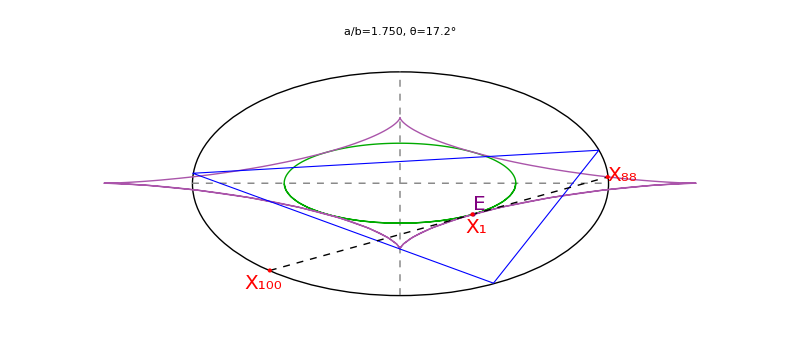

```mathematica
showX88complexLow[1.75,17.15,showX88complexObjs[1.75]]
```

```mathematica
DynamicModule[{objs},
Manipulate[
objs=showX88complexObjs[1.75];
Dynamic@showX88complexLow[1.75,tDeg,objs],
{{tDeg,10},-180,180,.5}]]
```

```mathematica
Clear@showX88complexTrioLow;showX88complexTrioLow[as_,tDegs_,objs123_]:=
Grid[{{
showX88complexLow[as[[1]],tDegs[[1]],objs123[[1]],slackX->.1,slackY->.15,size->475],
showX88complexLow[as[[2]],tDegs[[2]],objs123[[2]],slackX->.1,slackY->.15,size->500]},
{showX88complexLow[as[[3]],tDegs[[3]],objs123[[3]],slackY->.15],SpanFromLeft}},Frame->All]
```

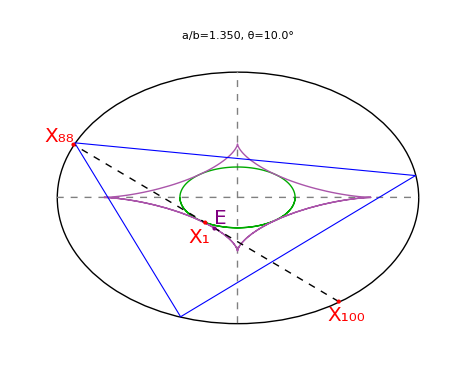
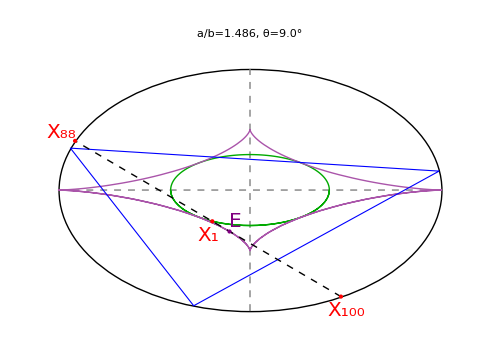
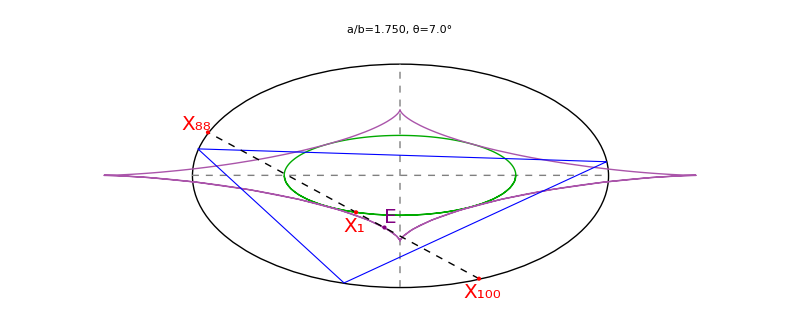
-Graphics- | -Graphics-
-Graphics- |

```mathematica
plotX88trio=Module[{objs123,as={1.35,1.486,1.75}},
objs123=showX88complexObjs/@as;
showX88complexTrioLow[as,{10,9.,7.},objs123]]
```

```mathematica
export4["1170_x88_trio",plotX88trio]
```

## Envelope of Gergonne and Antiorthic Axes

E(9) = isogonal conjugate of the antiorthic axis, [X(44),X (513)], with barycentric equation x + y + z = 0, 

Antiorthic passes through: [44?] 513, 649, 650, 652, 654, 656, 657, 659, 661, 672, 770, 798, 822, 851, 896, 899, 910, 1155, 1491, 1575, 1635, 1755, 2173, 2182, 2183, 2225, 2227, 2228, 2229, 2230, 2231, 2232, 2233, 2234, 2235, 2236, 2237, 2238, 2239, 2240, 2243, 2244, 2245, 2246, 2247, 2252, 2253, 2254, 2265, 2272, 2290, 2312, 2313, 2314, 2315, 2348, 2483, 2484, 2503, 2511, 2515, 2516, 2522, 2526, 2578, 2579, 2590, 2591, 2600, 2610, 2624, 2630, 2631, 2635, 2637, 2641, 2642, 3000, and 3013.

E(9) = isotomic conjugate of the Gergonne Line [L(55)] = [X(514),X(661)], with barycentric equation a x + b y + c z = 0.
Use X(693) instead of 514

Note: X(514) is isogConj(101) and isotConj(190): X(514) is the intersection of the Gergonne Line with the line at INFINITY 
Use X(693) = isotConj(100)
Note: X(661) is isog Conj(662), isotConj X(799)

Note: X(513) = isogConj(100) = intercept of antiorthic axis and the line at INFINITY (trilinear polars of X(1) and X(2))
Note: X(649) = isogConj(190) = Crossdifference of X(1) and X(2) = Trilinears    a(b - c) : b(c - a) : c(a - b)

X(656) = IsogConj(162) = CROSSDIFFERENCE OF X(1) AND X(19) =   (b^2 - c^2)(b^2 + c^2 - a^2) : :
X(673) =

#### A good pair close to the origin is X(857) = sinC^2 sin2B sin(C-A) + sinB^2 sin2C sin(B-A) X(908) = point acubens = (cosB + cosC-1)/a

```mathematica
getStats[magn[getX857Trilin@@Part[orbitNormals[1.5,toRad@#],{1,3}]]&/@Range[10,180,1]]
```

<|n→171,mean→3.15678,sd→0.460311,z→0.145817,min→2.6,max→3.9,median→3.05687|>

```mathematica
getStats[magn[getX908Trilin@@Part[orbitNormals[1.5,toRad@#],{1,3}]]&/@Range[10,180,1]]
```

<|n→171,mean→3.27336,sd→0.463293,z→0.141534,min→2.6,max→3.9,median→3.29012|>

```mathematica
getIsotMagn[a_,tDeg_]:=Module[{carts},
carts=getMosesIsotCartesians[Sequence@@Part[orbitNormals[a,toRad@tDeg],{1,3}],noIsot->True];
Transpose@{Second/@carts,magn/@(Third/@carts)}]
```

```mathematica
{Take[getIsotMagn[1.5,10.],3],Take[getIsotMagn[1.5,20],3]}
```

{{{514,0},{661,61.3591},{693,35.7108}},{{514,0},{661,47.866},{693,26.9615}}}

```mathematica
Module[{a=1.5,magns,ctrs,vals,stats},
magns=getIsotMagn[a,#]&/@Range[1,181,1];
ctrs=First/@magns[[1]];
vals=Transpose@Map[Second,magns,{2}];
stats=getStats/@vals;
List@@@Sort[MapThread[Join[<|"ctr"->#1|> ,#2]&,{ctrs,stats}],#1["mean"]<#2["mean"]&]]//Take[#,10]&//Grid
```

514 | 181 | 0 | 0 | 0 | 0 | 0 | 0
5179 | 181 | 3.15584 | 0.456244 | 0.144572 | 2.6 | 3.9 | 3.06105
5074 | 181 | 3.1572 | 0.456187 | 0.144491 | 2.6 | 3.9 | 3.06375
857 | 181 | 3.16305 | 0.461189 | 0.145805 | 2.6 | 3.9 | 3.06297
14206 | 181 | 3.17588 | 0.457449 | 0.144038 | 2.6 | 3.9 | 3.0993
14963 | 181 | 3.18417 | 0.460835 | 0.144727 | 2.6 | 3.9 | 3.11352
18715 | 181 | 3.21648 | 0.463097 | 0.143976 | 2.6 | 3.9 | 3.17741
908 | 181 | 3.28589 | 0.460043 | 0.140006 | 2.6 | 3.9 | 3.31614
1959 | 181 | 3.33647 | 0.457124 | 0.137008 | 2.6 | 3.9 | 3.41496
18669 | 181 | 3.36113 | 0.54364 | 0.161743 | 2.6 | 4.05551 | 3.36784

```mathematica
Sort[Append[#,magn@#[[2]]]&/@(Part[#,{2,3,4}]&/@getMosesIsotCartesians[Sequence@@Part[orbitNormals[1.5,toRad@20.],{1,3}],noIsot->True]),Last@#1<Last@#2&]//Take[#,30]&//Grid
```

514 | {0,0} | 190 | 0
5179 | {-0.956572,2.61568} |  | 2.7851
857 | {-1.02684,2.58998} |  | 2.78611
5074 | {-0.863934,2.64956} |  | 2.78685
14206 | {-1.28673,2.49494} | 2349 | 2.8072
14963 | {-1.31208,2.48567} |  | 2.81071
2583 | {-0.586775,2.75092} | 2581 | 2.8128
18715 | {-1.51378,2.4119} |  | 2.8476
18669 | {-0.12573,2.91952} |  | 2.92223
908 | {-1.8757,2.27955} |  | 2.95205
1959 | {-2.09323,2.19999} | 1821 | 3.03671
4766 | {-2.52293,2.04285} |  | 3.24629
30806 | {-2.54374,2.03524} | 1156 | 3.25773
4728 | {-2.78786,1.94596} | 4607 | 3.39984
3936 | {-2.82679,1.93173} | 24624 | 3.42379
3912 | {-3.15157,1.81295} | 673 | 3.63582
4486 | {-3.42698,1.71223} |  | 3.83092
3766 | {-3.46543,1.69817} | 660 | 3.85915
14210 | {-3.50317,1.68437} | 897 | 3.88707
4358 | {-3.81317,1.571} | 88 | 4.12412
3762 | {-4.08602,1.47122} | 3257 | 4.34281
3948 | {-4.12266,1.45782} |  | 4.37282
6381 | {-4.41913,1.3494} |  | 4.62056
30565 | {-4.75918,1.22504} |  | 4.91432
4462 | {3.26615,4.15996} | 27834 | 5.28895
14350 | {3.4016,4.20949} |  | 5.41209
3904 | {-6.10551,0.732675} | 655 | 6.14932
14207 | {4.24557,4.51814} |  | 6.19988
32679 | {-6.58036,0.559018} | 32680 | 6.60407
14209 | {-7.56847,0.19766} |  | 7.57105

```mathematica
newCenters[1.5,toRad@10.,{44}]
```

{{X(44),X(6)-LINE CONJUGATE OF X(1),{-2.28031,-2.76885}}}

```mathematica
Module[{ons},
ons=orbitNormals[1.5,toRad@100.];
{getX693Trilin[ons[[1]],ons[[3]]],
getX661Trilin[ons[[1]],ons[[3]]]}]
```

{{45.2173,6.10766},{-75.2509,-17.3815}}

#### Which isogs are small

```mathematica
Module[{o,n,s,mosesCtrs},
{o,n,s}=orbitNormals[1.5,toRad@.2];
mosesCtrs=Append[#,magn@#[[3]]]&/@getMosesCartesians[o,s,doIsog->True];
Sort[MapIndexed[Prepend[#1,First@#2]&,mosesCtrs],#1[[5]]<#2[[5]]&]]//Take[#,13]&//Grid
```

2 | 100 | ANTICOMPLEMENT OF FEUERBACH POINT | {0,0} | 0
16 | 1156 | ISOGONAL CONJUGATE OF X(1155) | {-3.54189,-0.0868923} | 3.54296
18 | 1821 | ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287) | {-3.54103,-0.118575} | 3.54301
31 | 24624 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2 | {-3.54226,-0.0733578} | 3.54302
11 | 673 | TRILINEAR POLE OF LINE X(1)X(514) | {-3.5426,-0.0610594} | 3.54312
15 | 897 | ISOGONAL CONJUGATE OF X(896) | {-3.5429,-0.0499984} | 3.54325
1 | 88 | ISOGONAL CONJUGATE OF X(44) | {-3.54309,-0.042904} | 3.54335
29 | 20332 | (name pending) | {-3.54356,-0.0256171} | 3.54365
19 | 2349 | X(2)-ISOCONJUGATE OF X(1495) | {-3.53787,-0.234641} | 3.54564
20 | 2580 | X(6)-ISOCONJUGATE OF X(2574) | {-3.54559,0.0487604} | 3.54592
30 | 23707 | ISOGONAL CONJUGATE OF X(2635) | {-3.53715,-0.260933} | 3.54676
14 | 823 | ISOGONAL CONJUGATE OF X(822) | {-3.89518,12.88} | 13.4561
7 | 655 | TRILINEAR POLE OF LINE X(1)X(5) | {-4.11538,20.9619} | 21.3621

```mathematica
getEnvelope[1.5,.2,getX44Trilin,getX1155Trilin,epsDeg->10^ -5]
```

{-3.54189,-0.0868923}

```mathematica
Module[{o,n,s,mosesCtrs},
{o,n,s}=orbitNormals[1.5,toRad@90.2];
mosesCtrs=Append[#,magn@#[[3]]]&/@getMosesCartesians[o,s,doIsog->True];
Sort[MapIndexed[Prepend[#1,First@#2]&,mosesCtrs],#1[[5]]<#2[[5]]&]]//Take[#,13]&//Grid
```

2 | 100 | ANTICOMPLEMENT OF FEUERBACH POINT | {0,0} | 0
16 | 1156 | ISOGONAL CONJUGATE OF X(1155) | {-0.0200912,3.362} | 3.36206
18 | 1821 | ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287) | {-0.0149926,3.36202} | 3.36206
31 | 24624 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2 | {-0.0238004,3.36198} | 3.36206
30 | 23707 | ISOGONAL CONJUGATE OF X(2635) | {-0.00875019,3.36206} | 3.36207
11 | 673 | TRILINEAR POLE OF LINE X(1)X(514) | {-0.0285966,3.36195} | 3.36207
19 | 2349 | X(2)-ISOCONJUGATE OF X(1495) | {-0.00743186,3.36206} | 3.36207
21 | 2581 | X(6)-ISOCONJUGATE OF X(2575) | {-0.00263906,3.36209} | 3.36209
15 | 897 | ISOGONAL CONJUGATE OF X(896) | {-0.0344799,3.36192} | 3.3621
1 | 88 | ISOGONAL CONJUGATE OF X(44) | {-0.0407025,3.36188} | 3.36213
29 | 20332 | (name pending) | {-0.0776005,3.36169} | 3.36258
32 | 27834 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71 | {175.59,4.30694} | 175.643
27 | 4607 | TRILINEAR POLE OF THE LINE X(1)X(190) | {-191.068,2.33399} | 191.082

```mathematica
getEnvelope[1.5,90.2,getX44Trilin,getX1155Trilin,epsDeg->10^ -4]
```

{-0.0200912,3.362}

```mathematica
showIsotCloud[a_,tDeg_]:=Module[{ell,gr,pts,ons,isots,isot1,isot2,bis,isogs,isog1,isog2},
ell=plotEllAxes[a,{Thick,Black}];
pts=Table[{a Cos@t,Sin@t},{t,0,π,π/40}];
ons=orbitNormals[a,toRad@tDeg];
{isot1,isot2}=#[ons[[1]],ons[[3]]]&/@{getX857Trilin,getX908Trilin};
{isog1,isog2}=#[ons[[1]],ons[[3]]]&/@{getX44Trilin,getX1155Trilin};
isots=isotomicConjugate[#,ons[[1]]]["pconj"]&/@pts;
bis=getTriBisectors@@ons[[1]];
isogs=isogonalConjugate[#,ons[[1]],bis]&/@pts;
gr=Graphics[{Thick,PointSize@Medium,FaceForm@None,
{EdgeForm@{Blue,Thick},Polygon@ons[[1]]},
{Red,Point@isots,Darker@Green,Point@isogs},
{Blue,Circle[#,.1]&/@{isot1,isot2}},
{Blue,Circle[#,.1]&/@{isog1,isog2}},
MapThread[Text[Subscript["X",#1],#2,{-1.5,-1.5}]&,{{857,908,44,1155},{isot1,isot2,isog1,isog2}}]}];
Show[{ell,gr}]];
```

```mathematica
Manipulate[Show[showIsotCloud[1.5,tDeg],PlotRange->{{-10,10},{-5,5}}],{{tDeg,10.},-180,180,.1}]
```

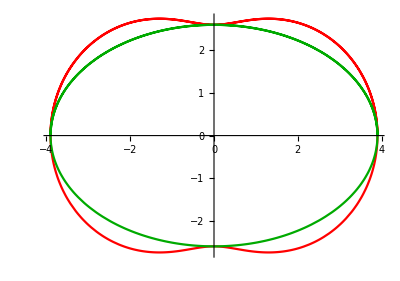

```mathematica
Module[{a=1.5,pp857,pp908,ons},
pp857=Quiet@ParametricPlot[ons=orbitNormals[a,t];getX857Trilin[ons[[1]],ons[[3]]],{t,0,π},PlotStyle->Red];
pp908=Quiet@ParametricPlot[ons=orbitNormals[a,t];getX908Trilin[ons[[1]],ons[[3]]],{t,0,π},PlotStyle->Darker@Green];
Show[{pp857,pp908}]]
```

#### X857 is not elliptic but X908 is. Report its axes

```mathematica
findEllParamsFn[1.5,getX857Trilin]["err"]
```

1.78065

```mathematica
findEllParamsFn[1.5,getX908Trilin]["err"]
```

8.10409×10^-14

```mathematica
getOrbitAxes[1.5,getX908Trilin]
```

{3.9,2.6}

```mathematica
getOrbitAxes[3,getX908Trilin]
```

{3.75,1.25}

#### Since envelope of antiorthic (resp. gergonne) coincides w/ locus of X1155 (resp. X908), drEnv -> False

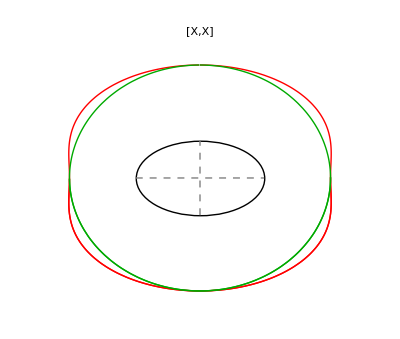
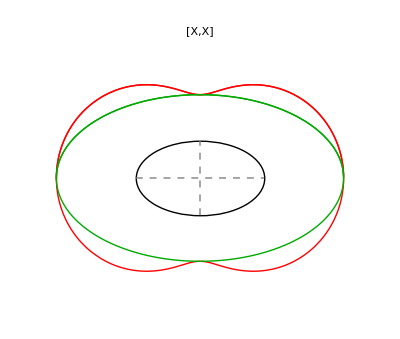
antiorthic | gergonne L(55)
-Graphics- | -Graphics-

```mathematica
(*Options@showEnvelopePairLow={slack->.05,perfGoal->"Quality",imgSize->800,"n1"->-1,"n2"->-1};*)
Module[{a=(1.+Sqrt@5)/2},Grid[{Style[#,{Blue,Bold,16}]&/@{"antiorthic","gergonne L(55)"},
{showEnvelopePairLow[a,getX44Trilin,getX1155Trilin,"n1"->44,"n2"->1155,slack->2.5,imgSize->400,drCirc->False,envDashed->True,drEnv->False],
(*showEnvelopePairLow[1.5,getX693Trilin,getX661Trilin,"n1"->693,"n2"->661,slack->2.5,imgSize->300]*)
showEnvelopePairLow[a,getX857Trilin,getX908Trilin,"n1"->857,"n2"->908,slack->2.5,imgSize->400,drCirc->False,envDashed->True,drEnv->False]
}}]]
```

```mathematica
getOrbitAxes[1.5,getX1155Trilin]
```

{3.54307,3.36205}

```mathematica
Clear@showGenericLineEnvelope;
Options@showGenericLineEnvelope={"n1"->857,"n2"->1155,imgSize->800,rayL->5,drC->True,displ->.1,drX4->False,addedGr->{},drEvolute->False};
showGenericLineEnvelope[a_,tDeg_,trilinFn1_,trilinFn2_,envPP_,OptionsPattern[]]:=Module[{ons,eps=.001,p1,p2,a2,b2,nhat,gr,env,nhatEvolute,evolute,v1,x1,x4},
ons=orbitNormals[a,toRad@(tDeg+eps)];
{p1,p2}=#[ons[[1]],ons[[3]]]&/@{trilinFn1,trilinFn2};
{a2,b2}=getOrbitAxes[a,trilinFn2];
nhat=norm[p1-p2];
env=getEnvelope[a,tDeg,trilinFn1,trilinFn2];
(* ellipse evolute is envelope of line from one vertex to the incenter *)
evolute=getEnvelope[a,tDeg,getIncenterTrilin,Function[{o,s},o[[1]]]];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
x4=getOrthocenterTrilin[ons[[1]],ons[[3]]];
v1=ons[[1,1]];
nhatEvolute=norm[x1-v1];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{Purple,Thick,Line@{p1,ray[p1,nhat,OptionValue@rayL]},Line@{p2,ray[p2,-nhat,OptionValue@rayL]},Line@{p1,p2}},
If[OptionValue@drEvolute,{Lighter@Brown,Thick,Line@{v1,ray[v1,nhatEvolute,OptionValue@rayL]},Line@{x1,ray[x1,-nhatEvolute,OptionValue@rayL]},Line@{v1,x1},Point@evolute},{}],
{Red,Point@p1,Darker@Green,Point@p2},
{Darker@Red,Point@{0,0},Text[Style["X_9",20],{0,0},{-1.5,1.5}]},
{Purple,Point@env,If[OptionValue@drC,ellLabelTxtb[a2,b2,env,Style["C",20],OptionValue@displ,inward->True],{}]},
If[OptionValue@drX4,{Orange,Point@x4},{}],
MapThread[ellLabelTxtb[a2,b2,#2,Style[Subscript["X",#1],20],OptionValue@displ]&,{{OptionValue@"n1",OptionValue@"n2"},{p1,p2}}]}];
Show[{envPP,gr,OptionValue@addedGr},ImageSize->OptionValue@imgSize,PlotLabel->Style["a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°",{Black,20}]]];
```

```mathematica
DynamicModule[{a=1.618,envGergonne,envAntiorthic},
Manipulate[
envAntiorthic=showEnvelopePairLow[a,getX44Trilin,getX1155Trilin,perfGoal->"Quality","n1"->44,"n2"->1155,slack->3.,imgSize->800,drCirc->False,envDashed->True];
envGergonne=showEnvelopePairLow[a,getX857Trilin,getX908Trilin,perfGoal->"Quality","n1"->857,"n2"->908,slack->3.,imgSize->400,drCirc->False,envDashed->True];
Dynamic@Grid[{
Style[#,{Blue,20}]&/@{"Isogonal: Antiorthic Axis (X_44,X_(1155))","Isotomic: Gergonne Line (X_857,X_908)"},
{showGenericLineEnvelope[a,tDeg,getX44Trilin,getX1155Trilin,envAntiorthic,"n1"->44,"n2"->1155,rayL->4,imgSize->600,displ->.2],
showGenericLineEnvelope[a,tDeg,getX857Trilin,getX908Trilin,envGergonne,"n1"->857,"n2"->908,rayL->4,imgSize->600,displ->.2]}},Frame->All],{{tDeg,-60.},-180,180,.1}]]
```

```mathematica
showConjEnvPair[a_,tDeg_]:=Module[{envAntiorthic,envGergonne},envAntiorthic=showEnvelopePairLow[a,getX44Trilin,getX1155Trilin,perfGoal->"Quality","n1"->44,"n2"->1155,slack->3.,imgSize->800,drCirc->False,envDashed->True];
envGergonne=showEnvelopePairLow[a,getX857Trilin,getX908Trilin,perfGoal->"Quality","n1"->857,"n2"->908,slack->3.,imgSize->400,drCirc->False,envDashed->True];
Grid[{
Style[#,{Blue,24}]&/@{"Isogonal: Antiorthic Axis (X_44,X_1155)","Isotomic: Gergonne Line (X_857,X_908)"},
{showGenericLineEnvelope[a,tDeg,getX44Trilin,getX1155Trilin,envAntiorthic,"n1"->44,"n2"->1155,rayL->4,imgSize->600,displ->.3],
showGenericLineEnvelope[a,tDeg,getX857Trilin,getX908Trilin,envGergonne,"n1"->857,"n2"->908,rayL->4,imgSize->600,displ->.3]}},Frame->All]];
```

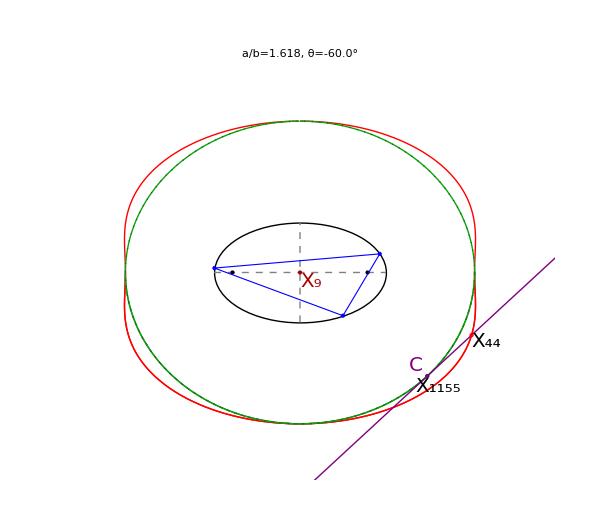
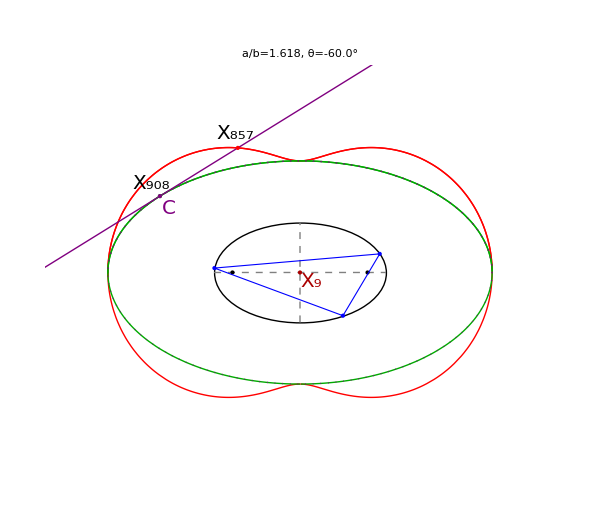
Isogonal: Antiorthic Axis (X_44,X_1155) | Isotomic: Gergonne Line (X_857,X_908)
-Graphics- | -Graphics-

```mathematica
conjEnvPlot=showConjEnvPair[1.618,-60]
```

```mathematica
export4["1180_conj_env_pair",conjEnvPlot]
```

## Evolute of Ellipse and Envelope of Vertex with Triangle Center

#### Ronaldo, 27/feb/2019: Four points the ellipse evolute touches the X1 locus

```mathematica
evoluteX1touch[a_,b_]:=Module[{a2=a*a,b2=b*b,c2,delta,x,y},
c2=a2-b2;
delta=Sqrt[a2^2-a2*b2+b2^2];
x=c2((-b2+delta)/c2)^(3/2)/a;
y=c2((a^2-delta)/c2)^(3/2)/b;
{x,y}]
```

#### Envelope of X1 and X5 touches the X1 locus at the same place, ~52.4 degrees for a/b = 1.618

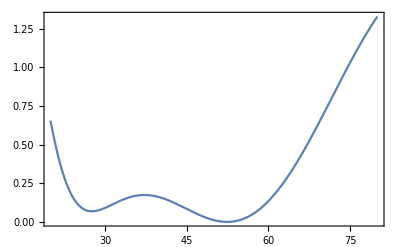

```mathematica
Module[{a=1.618},
Plot[magn2[getEnvelope[a,theta,getIncenterTrilin,getNinepointCenterTrilin]-evoluteX1touch[a,1]],{theta,20,80},Frame->True]]
```

```mathematica
Module[{a=1.618,theta=52.38,evoContact},
evoContact=evoluteX1touch[a,1];magn2[getEnvelope[a,theta,getIncenterTrilin,getNinepointCenterTrilin]-evoContact]]
```

0.0000100652

#### FindMinimum not working

```mathematica
Module[{a=1.618,evoContact},
evoContact=evoluteX1touch[a,1];
FindMinimum[magn2[getEnvelope[a,theta,getIncenterTrilin,getNinepointCenterTrilin]-evoContact],
{theta,52.}]]
```

{0.317724,{theta→60.6455}}

```mathematica
DynamicModule[{a=1.618,envX1X5,envTouchX1,envTouchX1gr,ellCaustic},
Manipulate[
envX1X5=showEnvelopePairLow[a,getIncenterTrilin,getNinepointCenterTrilin,
perfGoal->"Speed","n1"->1,"n2"->5,slack->.5,imgSize->800,drCirc->False,drEvolute->True];
envTouchX1=evoluteX1touch[a,1];
ellCaustic=plotEllb[Sequence@@getCausticAxes[a,1],{Brown,Thick}];
envTouchX1gr={(*ellCaustic,*)Graphics[{Blue,PointSize@Large,Point@{envTouchX1,flipX@envTouchX1,flipY@envTouchX1,-envTouchX1}}]};
Dynamic@Grid[{
{showGenericLineEnvelope[a,tDeg,getIncenterTrilin,getNinepointCenterTrilin,envX1X5,drEvolute->True,
"n1"->1,"n2"->5,addedGr->envTouchX1gr,drC->False,rayL->4,imgSize->600,drX4->True]}},Frame->All],{{tDeg,-60.},-180,180,.05}]]
```

#### Evolute of Billiard

```mathematica
Clear@getEvoluteTriangle;
getEvoluteTriangle[a_,tDeg_,trilinFn_]:=Module[{ons,ev1,ev2,ev3},
ons=orbitNormals[a,toRad@tDeg];
ev1=getEnvelope[a,tDeg,trilinFn,Function[{o,s},o[[1]]]];
ev2=getEnvelope[a,tDeg,trilinFn,Function[{o,s},o[[2]]]];
ev3=getEnvelope[a,tDeg,trilinFn,Function[{o,s},o[[3]]]];
{ev1,ev2,ev3}];
```

```mathematica
Clear@ellEvoluteTrilin;
Options@ellEvoluteTrilin={slack->.1,clr->{Thick,Dashed,Blue},"n"->-1,drCaustic->False,causticClr->{Thick,Brown}};
ellEvoluteTrilin[a_,trilinFn_,OptionsPattern[]]:=Module[{c2=a^2-b^2,pp,ell,ellCaustic,foci,gr,pr,ons,pl},
foci=getFoci[a];
ell=plotEllAxes[a,{Thick,Black}];
ellCaustic=If[OptionValue@drCaustic,plotEllb[Sequence@@getCausticAxes[a,1],OptionValue@causticClr],{}];
gr=Graphics[{PointSize@Medium,Point@foci}];
pp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg];getEnvelope[a,tDeg,trilinFn,Function[{o,s},o[[1]]]],{tDeg,0,360},
PerformanceGoal->"Speed",PlotStyle->OptionValue@clr];
pl="a/b="<>nfn[a,2]<>", "<>ToString[Subscript["X",OptionValue@"n"],StandardForm];
pr={{-a-OptionValue@slack,a+OptionValue@slack},{-1-OptionValue@slack,1+OptionValue@slack}};
Show[{ell,ellCaustic,gr,pp},PlotRange->pr,PlotLabel->Style[pl,{Black,16}]]];
```

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,x144→-Graphics-,x59→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,x100→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
Clear@ellEvoluteGrid;
Options@ellEvoluteGrid={cols->4,imgSize->400,maxX->2,maxY->1.25};
ellEvoluteGrid[a_,{ns_,fns_,clrs_},OptionsPattern[]]:=Grid[Partition[MapThread[Show[ellEvoluteTrilin[a,#1,"n"->#2,
clr->{Thick,#3/.ptClrs}],PlotRange->{{-OptionValue@maxX,OptionValue@maxX},{-OptionValue@maxY,OptionValue@maxY}},ImageSize->OptionValue@imgSize]&,
{fns,ns,clrs}],OptionValue@cols],Spacings->{0,0},Frame->All];
```

```mathematica
showOneEvoluteGrid[a_]:=ellEvoluteGrid[a,Transpose@{
{1,getIncenterTrilin,"inc"},
{2,getBarycenterTrilin,"bar"},
{3,getCircumcenterTrilin,"cir"},
{4,getOrthocenterTrilin,"ort"},
{5,getNinepointCenterTrilin,"npc"},
{6,getSymmedianTrilin,"sym"},
{7,getNagelTrilin,"nag"},
{8,getGergonneTrilin,"ger"},
{10,getSpiekerTrilin,"spi"},
{11,getFeuerbachTrilin,"feu"},
{12,getX12Trilin,"x88"},
{20,getX20Trilin,"bev"}},cols->4];
```

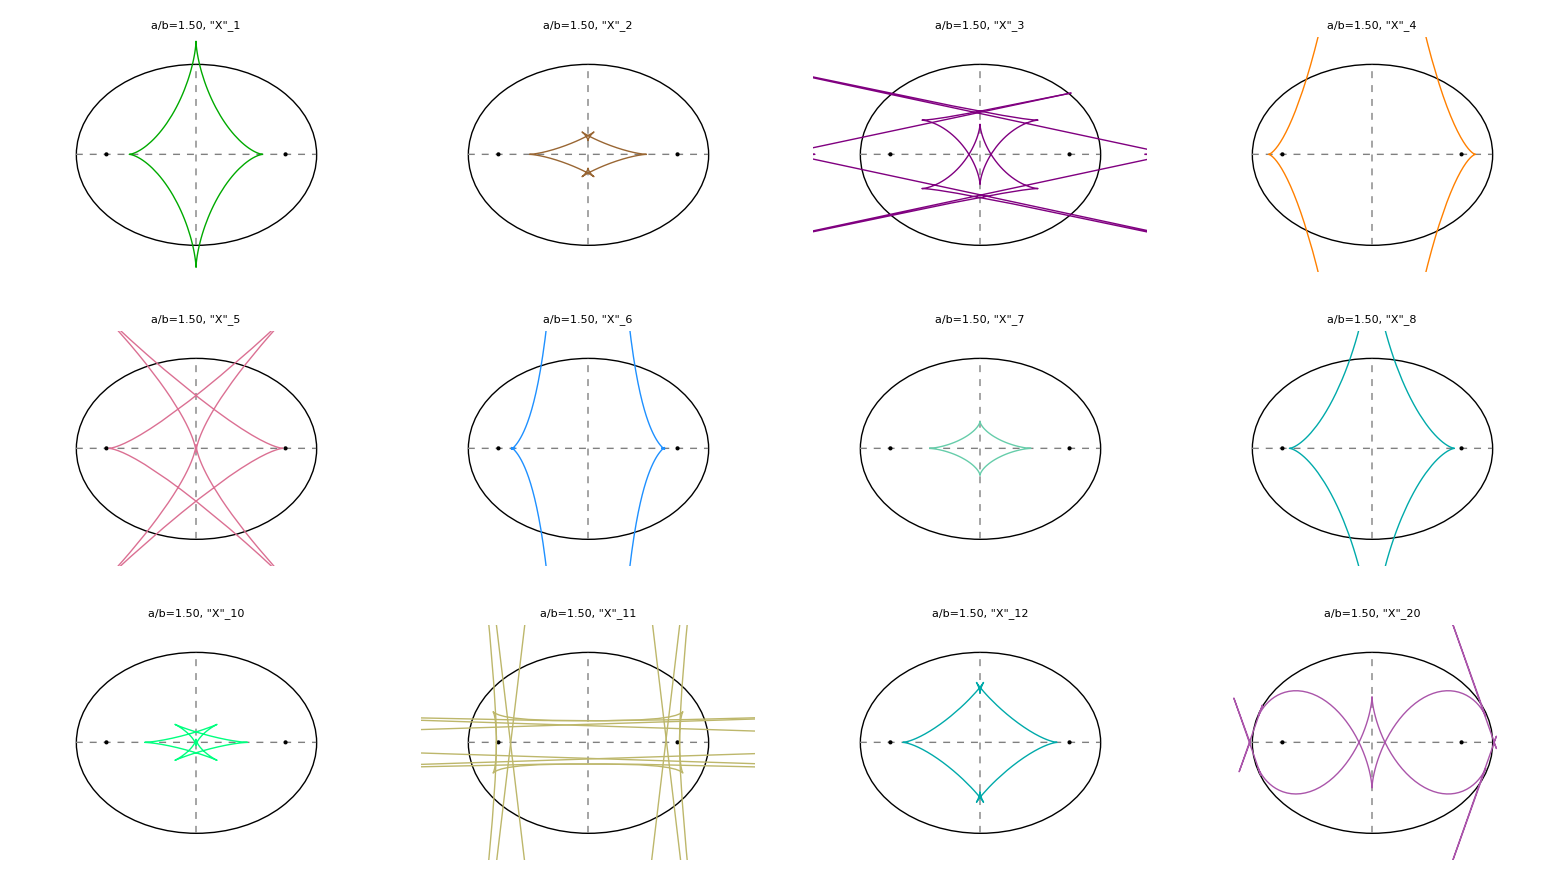

```mathematica
showOneEvoluteGrid[1.5]
```

## Evolute Triangle

```mathematica
Clear@showEvoluteTriangle;
Options@showEvoluteTriangle={clr->Thick@Purple,locusClr->{Thick,Darker@Green},triClr->{Thick,Pink},drStats->True,"n"->-1,imgSize->400,slackX->.1,slackY->.1,drCaustic->False};
showEvoluteTriangle[a_,tDeg_,trilinFn_,OptionsPattern[]]:=Module[{ons,gr,evTri,evTriSides,ell,ellCaustic,ellEv,xi,locus,maxY,pl,evr,evR,evA,r,R,A,pr,fs},
ell=plotEllAxes[a,{Black,Thick}];
ellCaustic=If[OptionValue@drCaustic,plotEllb[Sequence@@getCausticAxes[a,1],{Thick,Brown}],{}];
ellEv=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg2];getEnvelope[a,tDeg2,trilinFn,Function[{o,s},o[[1]]]],{tDeg2,0,360},
PerformanceGoal->"Speed",PlotStyle->OptionValue@clr];
locus=Quiet@ParametricPlot[ons=orbitNormals[a,t];trilinFn[ons[[1]],ons[[3]]],{t,0,π},
PerformanceGoal->"Speed",PlotStyle->OptionValue@locusClr];
maxY=getEvoluteTriangle[a,-90,trilinFn][[1,2]];
ons=orbitNormals[a,toRad@tDeg];
xi=trilinFn[ons[[1]],ons[[3]]];
r=getInradius@ons[[3]];
R=getCircumradius@ons[[3]];
A=-signedArea[ons[[1]]];
evTri=getEvoluteTriangle[a,tDeg,trilinFn];
evTriSides=triLengths@evTri;
evr=getInradius@evTriSides;
evR=getCircumradius@evTriSides;
evA=signedArea[evTri];
fs=getFoci[a];
gr=Graphics[{PointSize@Large,FaceForm@None,
{PointSize@Medium,Black,Point@{0,0},Point@fs},
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{EdgeForm[OptionValue@triClr],Polygon@evTri,Sequence@@OptionValue@triClr,Point@evTri},
{Darker@Green,Point@xi},
{Gray,Line@{#,xi}&/@ons[[1]],Line@{xi,#}&/@evTri}}];
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
(*{Min[-maxY-OptionValue@slackY,-1-OptionValue@slackY],Max[maxY+OptionValue@slackY,1+OptionValue@slackY]}};*)
pl=ToString[Style[Subscript["X",OptionValue@"n"],Bold],StandardForm]<>": a/b="<>nfn[a,2]<>", θ="<>nfn[N@tDeg,1]<>"°"<>If[!OptionValue@drStats,"","\n"<>
"r="<>nfn[r,2]<>", R="<>nfn[R,2]<>", r/r_ev="<>nfn[r/evr,2]<>", r*r_ev="<>nfn[r*evr,2]<>"\n"<>
"r_ev="<>nfn[evr,2]<>", R_ev="<>nfn[evR,2]<>", r_ev/R_ev="<>nfn[evr/evR,2]<>", r_ev*R_ev="<>nfn[evr*evR,2]<>"\n"<>
"A="<>nfn[A,2]<>", A_ev="<>nfn[evA,2]<>", A/A_ev="<>nfn[A/evA,2]<>", A*A_ev="<>nfn[A*evA,2]];
Show[{ell,ellCaustic,locus,ellEv,gr},PlotLabel->Style[pl,{16,Black}],Axes->False,PlotRange->pr,ImageSize->OptionValue@imgSize]];
```

```mathematica
showEvTris[a_,tDeg_]:=Partition[MapThread[showEvoluteTriangle[a,tDeg,#2,"n"->#1,slackY->.2,drStats->False,clr->{Dashed,Purple},triClr->{Thickness@.0075,Pink},imgSize->400]&,Transpose@{
{1,getIncenterTrilin},
{3,getBarycenterTrilin},
{5,getNinepointCenterTrilin},
{20,getX20Trilin}
}],2]//Grid[#,Frame->All]&
```

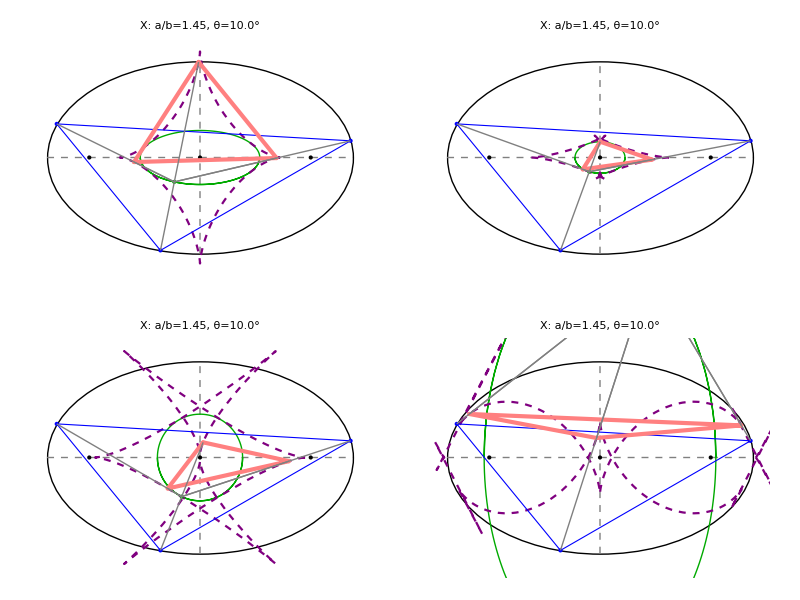

```mathematica
showEvTris[1.45,10.]
```

## Evolutes from Orbit Vertex to Vertex of Derived Tri

```mathematica
triFns={
{"intouch",intouchTriangle},
{"extouch",extouchTriangle},
{"excentral",excentralTriangle},
{"incentral",incentralTriangle},
{"orthic",orthicTriangle},
{"medial",medialTriangle},
{"anticompl",anticomplementaryTriangle},
{"feuerbach",feuerbachTriangle},
{"euler",eulerTriangle},
{"symmedial",symmedialTriangle},
{"yff",yffTriangle},
{"tangential",tangentialTriangle},
{"ext.tangs.",externaltangentsTriangle},
{"hexyl",hexylTriangle},
{"outer nap.",outerNapoleonTriangle},
{"1st morley",firstMorleyTriangle},
{"2nd morley",secondMorleyTriangle},
{"3rd morley",thirdMorleyTriangle}};
```

```mathematica
triFnsAssoc=Association[Rule[#[[1]],#[[2]]]&/@triFns];
```

#### Needs getEnvelope[] above

```mathematica
getVtxToVtxEvolute[a_,fn_]:=ellEvoluteTrilin[a,fn[#1,#2][[1]]&,drCaustic->True,clr->Blue]
```

```mathematica
getVtxToVtxEvolute2[a_,fn_]:=ellEvoluteTrilin[a,fn[#1,#2][[2]]&,drCaustic->True,clr->Red]
```

```mathematica
Options@getEnvelope
```

{epsDeg→0.001,tDeg2Phase→0}

```mathematica
Clear@ellEvoluteTrilinPair;
Options@ellEvoluteTrilinPair={slack->.1,clr->{Thick,Dashed,Blue},"n"->-1,drCaustic->False,tDeg2Phase->0};
ellEvoluteTrilinPair[a_,trilinFn1_,trilinFn2_,opts:OptionsPattern[]]:=Module[{c2=a^2-b^2,pp,ell,ellCaustic,foci,gr,pr,ons,pl},
foci=getFoci[a];
ell=plotEllAxes[a,{Thick,Black}];
ellCaustic=If[OptionValue@drCaustic,plotEllb[Sequence@@getCausticAxes[a,1],{Thick,Brown}],{}];
gr=Graphics[{PointSize@Medium,Point@foci}];
(*pp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg];getEnvelope[a,tDeg,trilinFn1,trilinFn2,FilterRules[{opts},Options@getEnvelope]],{tDeg,0,360},
PerformanceGoal->"Speed",PlotStyle->OptionValue@clr];*)
pp=getEnvelopeLocus[a,trilinFn1,trilinFn2,OptionValue@clr,FilterRules[{opts},Options@getEnvelopeLocus]];
pl="a/b="<>nfn[a,2];
pr={{-a-OptionValue@slack,a+OptionValue@slack},{-1-OptionValue@slack,1+OptionValue@slack}};
Show[{ell,ellCaustic,gr,pp},PlotRange->pr,PlotLabel->Style[pl,{Black,16}]]];
```

```mathematica
Clear@getVtxToVtxEvolutePair;
Options@getVtxToVtxEvolutePair=Options@ellEvoluteTrilinPair;
getVtxToVtxEvolutePair[a_,fn1_,fn2_,opts:OptionsPattern[]]:=ellEvoluteTrilinPair[a,fn1[#1,#2][[1]]&,fn2[#1,#2][[1]]&,
FilterRules[{opts,drCaustic->True,clr->Blue},Options@ellEvoluteTrilinPair]];
```

```mathematica
Clear@getVtxToVtxEvolutePair2;
getVtxToVtxEvolutePair2[a_,fn1_,fn2_,opts:OptionsPattern[]]:=ellEvoluteTrilinPair[a,fn1[#1,#2][[1]]&,fn2[#1,#2][[2]]&,
FilterRules[{opts,drCaustic->True,clr->Red},Options@ellEvoluteTrilinPair]];
```

```mathematica
(* gives straight line *)
Clear@getVtxToVtxEvolutePair90;getVtxToVtxEvolutePair90[a_,fn_,opts:OptionsPattern[]]:=ellEvoluteTrilinPair[a,fn[#1,#2][[1]]&,fn[#1,#2][[1]]&,FilterRules[{opts,tDeg2Phase->90,drCaustic->True,clr->Purple},Options@ellEvoluteTrilinPair]];
Clear@getVtxToVtxEvolutePair90duo;
getVtxToVtxEvolutePair90duo[a_,fn1_,fn2_,opts:OptionsPattern[]]:=ellEvoluteTrilinPair[a,fn1[#1,#2][[1]]&,fn2[#1,#2][[1]]&,FilterRules[{opts,tDeg2Phase->90,drCaustic->True,clr->Darker@Green},Options@ellEvoluteTrilinPair]];
```

## Orbit P1 to derived P1'

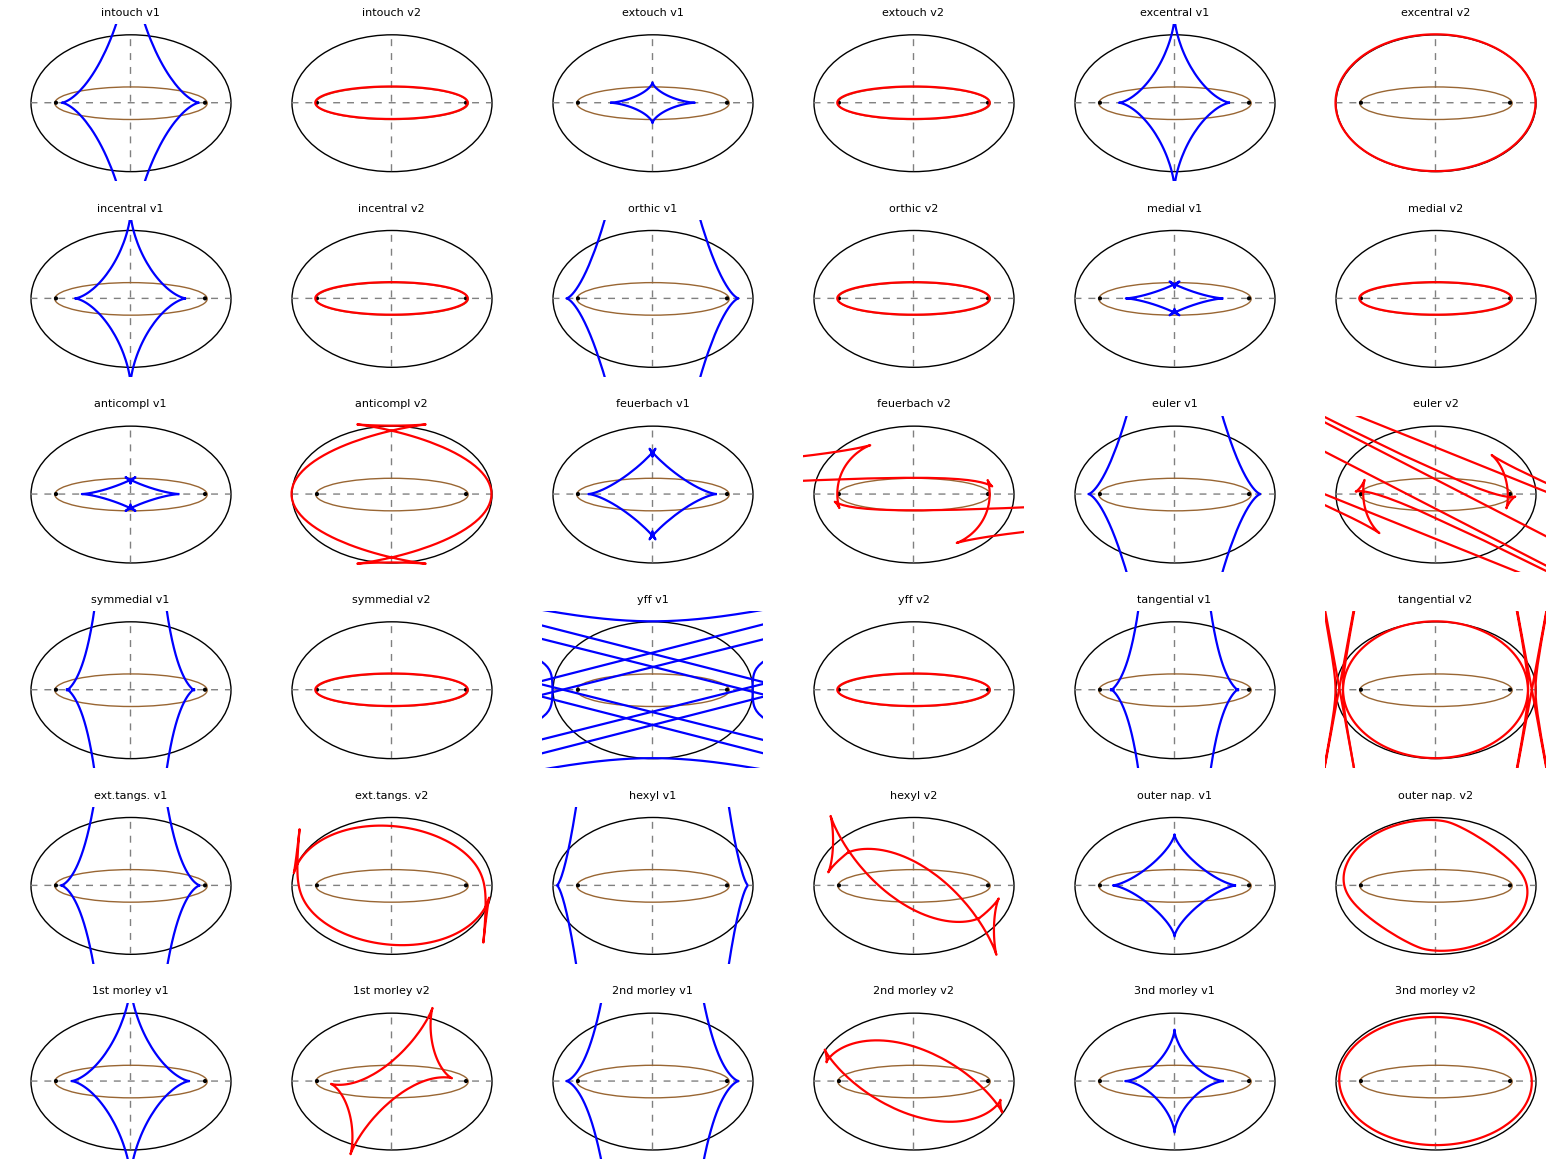

```mathematica
Module[{a=1.5},
Grid[Partition[Flatten@Transpose@{
Show[getVtxToVtxEvolute[a,#[[2]]],PlotLabel->Style[(#[[1]]<>" v1"),{16,Black}]]&/@triFns,
Show[getVtxToVtxEvolute2[a,#[[2]]],PlotLabel->Style[(#[[1]]<>" v2"),{16,Black}]]&/@triFns},6]]]
```

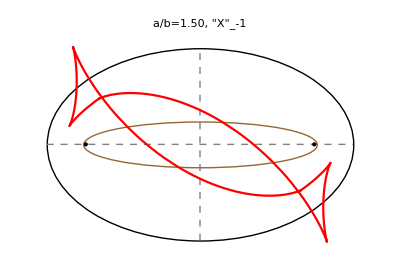

```mathematica
getVtxToVtxEvolute2[1.5,hexylTriangle]
```

## Tri1 P1 with Tri2 Q1

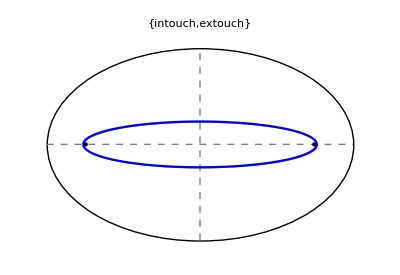
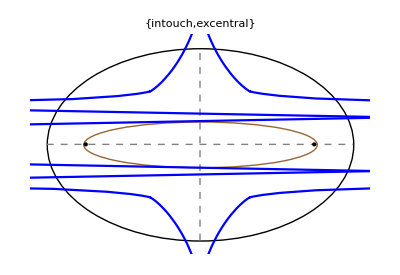
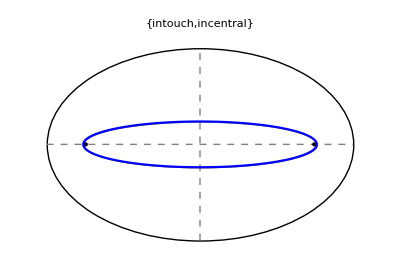
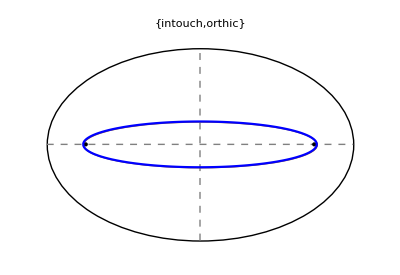
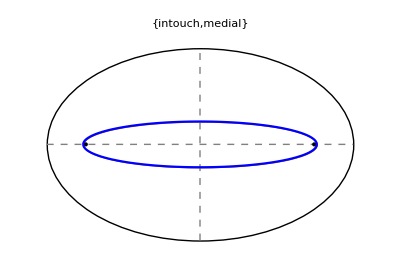
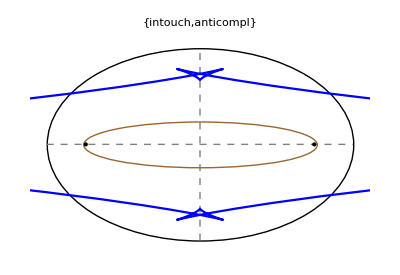
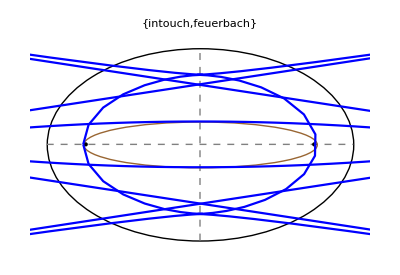
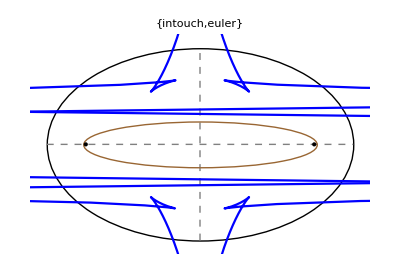
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{a=1.5,tups},
tups=Subsets[triFns,{2}];
Show[getVtxToVtxEvolutePair[1.5,#[[1,2]],#[[2,2]]],PlotLabel->Style[First/@#,16]]&/@Take[tups,All]]
```

#### Best-Of

```mathematica
Module[{pairs={
{"excentral","yff"},
{"yff","3rd morley"},
{"anticompl","yff"}
}},
Grid[{Show[getVtxToVtxEvolutePair[1.5,Sequence@@triFnsAssoc/@#],PlotLabel->Style[#,{Black,16}],ImageSize->200,PlotRange->All]&/@pairs}]]
```

-Graphics- | -Graphics- | -Graphics-

## Tri1 P1 with Tri2 Q2

```mathematica
Module[{a=1.5,tups},
tups=Subsets[triFns,{2}];
Show[getVtxToVtxEvolutePair2[a,#[[1,2]],#[[2,2]]],PlotLabel->Style[First/@#,16]]&/@Take[tups,All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## New: Tri1 P1 with Tri1 P2

```mathematica
Take[triFns,3]
```

{{intouch,intouchTriangle},{extouch,extouchTriangle},{excentral,excentralTriangle}}

```mathematica
Clear@trisP1P2;
Options@trisP1P2={slackX->.5,slackY->1};
trisP1P2[a_,OptionsPattern[]]:=Module[{pr,toShow},
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
toShow=Show[getVtxToVtxEvolutePair2[a,#[[2]],#[[2]]],PlotRange->pr,PlotLabel->Style[#[[1]],16]]&/@Take[triFns,All];Grid[{{Style["a/b="<>nfn[a,3],{Bold,20}],SpanFromLeft},Sequence@@Partition[toShow,4]},Alignment->Center,Frame->All]];
```

```mathematica
trisP1P2[1.618]
```

a/b=1.618 |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

## Tri1 P1 with Tri2 Q1' rot 90

```mathematica
getVtxToVtxEvolutePair90[1.5,intouchTriangle]
```

-Graphics-

```mathematica
getVtxToVtxEvolutePair90[1.5,#[[2]]]&/@triFns
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{a=1.5,tups},
tups=Subsets[triFns,{2}];
Show[getVtxToVtxEvolutePair90duo[1.5,#[[1,2]],#[[2,2]]],PlotLabel->Style[First/@#,16]]&/@Take[tups,All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Envelope Orbit [P1(t), P1(t+π/2)]: Affine Ellipse

```mathematica
getVtxToVtx90Axes[a_]:=Module[{envL,envT,fn1=Function[{o,s},o[[1]]]},
envL=getEnvelope[a,-45,fn1,fn1,tDeg2Phase->90.];
envT=getEnvelope[a,45,fn1,fn1,tDeg2Phase->90.];
{envL[[1]],envT[[2]]}]
```

```mathematica
Clear@vtxToVtx90Frame;vtxToVtx90Frame[a_,tDeg_,duoEv_]:=Module[{ons,ons90,env,ps,gr,ratio,pl,pr,slack=.2,x4,fn1=Function[{o,s},o[[1]]],foci},
ons=orbitNormals[a,toRad@tDeg];
ons90=orbitNormals[a,toRad@(tDeg+90)];
env=getEnvelope[a,tDeg,fn1,fn1,tDeg2Phase->90.];
ps={ons[[1,1]],ons90[[1,1]]};
x4=getOrthocenterTrilin[ons[[1]],ons[[3]]];
foci=getFocib@@getVtxToVtx90Axes[a];
gr=Graphics[{PointSize@Large,FaceForm@None,
{Darker@Green,Point@foci},
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{EdgeForm@{Thick,Dashed,Blue},Polygon@ons90[[1]]},
{Red,Point@env,Thick,Line@ps,Point@ps,Text[Style["C",20],env,{0,-1.5}]},
{Blue,ellLabelTxt[a,ps[[1]],Style["P",20],.1],ellLabelTxt[a,ps[[2]],Style["P_90",20],.1]},
{Orange,Point@x4,Text[Style["X_4",20],x4,{0,-1.5}]}}];
ratio=magn[env-ps[[1]]]/magn[ps[[1]]-ps[[2]]];
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"\n|C-P|/|P_90-P|="<>nfn[ratio,2];
pr={{-a-slack,a+slack},{-1-slack,1+slack}};
Show[{duoEv,gr},PlotRange->pr,ImageSize->800,PlotLabel->Style[pl,{Black,16}]]];
```

It is similar to billiard, by affine argument: let P1’=[a cos(t+π/2), b sin(t+π/2)]=[a sin(t), -b cos(t)].
 divide x by a/b and get:

P1 = [b cos(t), b sin(t)]
P1’ = [b sin(t), -b cos(t)]

both are on same circle, 3-periodics are equilaterals. connecting their vertices one is tangent to a their incircle, at the midpoint of chord.  invert affine: incircle becomes elliptic locus and tangent point is always halfway between P1 and P1’.

```mathematica
Module[{a=1.5,env,fn1=Function[{o,s},o[[1]]],locus},
locus=Table[getEnvelope[a,tDeg,fn1,fn1,tDeg2Phase->90.],{tDeg,0,360,10}];
findEllParams[a,-1,locus,"envelope P1 with P1+90"]]
```

<|i→-1,name→envelope P1 with P1+90,errNegl→True,ellSim→True,ellSimInv→False,ellEq→False,ellEqInv→False,causticSim→False,causticSimInv→False,causticEq→False,causticEqInv→False,confocal→False,err→1.79716×10^-12,a→1.5,b→1,a/b→1.5,b/a→0.666667,c→1.11803,lsc2→0.790569,lsA→1.06066,lsB→0.707107,lsA/lsB→1.5,lsB/lsA→0.666667,caustic_a→1.14307,caustic_b→0.23795,caustic_a/b→4.80384,caustic_b/a→0.208167,caustic_c→1.11803|>

```mathematica
DynamicModule[{a=1.5,duo,gr,env,fn=Function[{o,s},o]},
Manipulate[
duo=getVtxToVtxEvolutePair90[a,fn,clr->{Thick,Darker@Green}];
Dynamic@vtxToVtx90Frame[a,tDeg,duo],{{tDeg,0.},-180,180.,1}]]
```

```mathematica
getEllParamsV1negV2[a_]:=Module[{env,fn1=Function[{o,s},o[[1]]],locus},
locus=Table[getEnvelope[a,tDeg,fn1,Function[{o,s},-o[[3]]],tDeg2Phase->0.],{tDeg,0,360,10}];
findEllParams[a,-1,locus,"envelope P1 with - P2"]]
```

```mathematica
getEllParamsV1negV2[1.5]
```

<|i→-1,name→envelope P1 with - P2,errNegl→True,ellSim→False,ellSimInv→False,ellEq→False,ellEqInv→False,causticSim→False,causticSimInv→False,causticEq→False,causticEqInv→False,confocal→False,err→5.73145×10^-10,a→1.5,b→1,a/b→1.5,b/a→0.666667,c2→1.25,lsc2→1.70332,lsA→1.45692,lsB→0.647518,lsA/lsB→2.25,lsB/lsA→0.444444,caustic_a→1.14307,caustic_b→0.23795,caustic_a/b→4.80384,caustic_b/a→0.208167,caustic_c→1.11803|>

## Ronaldo: Envelope of Orbit [P1,-P2]

```mathematica
Clear@makeOneV1negV2frame;makeOneV1negV2frame[a_,tDeg_,evLocus_,evParams_,slack_:.2]:=Module[{evFoci,ons,env,gr,pr,pl},
evFoci={{-Sqrt@evParams["lsc2"],0},{Sqrt@evParams["lsc2"],0}};
ons=orbitNormals[a,toRad@tDeg];
env=getEnvelope[a,tDeg,Function[{o,s},o[[1]]],Function[{o,s},-o[[2]]]];
gr=Graphics[{FaceForm@None,PointSize@Large,AbsoluteThickness[3],
{EdgeForm@{AbsoluteThickness[3],Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{EdgeForm@{AbsoluteThickness[3],Dashed,Blue},Polygon@(-ons[[1]]),Blue,Point@(-ons[[1]])},
{Red,Line@{ons[[1,1]],-ons[[1,2]]},Point@{ons[[1,1]],-ons[[1,2]]}},
{Darker@Green,PointSize@Medium,Point@evFoci},
{Blue,ellLabelPoints[a,ons[[1]],"P",20,.1]},
{Blue,ellLabelPoints[a,-ons[[1]],"-P",20,.1]},
(*ellLabelTxtb[a_,b_,p_,txt_,lgt_,opts:OptionsPattern[]]*)
{Red,Point@env,ellLabelTxtb[evParams["lsA"],evParams["lsB"],env,Style["C",20],.066]}}];
pr={{-a-slack,a+slack},{-1-slack,1+slack}};
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°";
Show[{evLocus,gr},PlotLabel->Style[pl,{Black,20}],ImageSize->800,PlotRange->pr]];
```

```mathematica
DynamicModule[{a=1.5,evLocus,params,evParams},
Manipulate[
evParams=getEllParamsV1negV2[a];
evLocus=ellEvoluteTrilin[a,Function[{o,s},-o[[2]]],clr->{AbsoluteThickness[3],Darker@Green},drCaustic->True,causticClr->{AbsoluteThickness[3],Brown}];
Dynamic@makeOneV1negV2frame[a,tDeg,evLocus,evParams],{{tDeg,10.},-180,180,.1}]]
```

## Make Movies

```mathematica
doEnvelopesP1P2=True;
If[doEnvelopesP1P2,
Module[{imgs,amax=2},
imgs=Table[trisP1P2[a,slackX->(2.1-a),slackY->1],{a,1.1,amax,.002}];
makeMovie["envelopes p1p2 v4.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 1804 frames to envelopes p1p2 v4.mov

```mathematica
doBatman2=False;
If[doBatman2,
Module[{sz=1200,a=(Sqrt@5+1)/2.,pg="Quality",degStep=.25,
as,imgsPre,imgsPreRot,(*imgsPost,*)imgsRotate,imgsAll,imgBat90,imgsPostMix,imgsBatA,batmanPreEnv,batmanPostEnv},
Print["Make pre and post backdrops...",Now];
batmanPreEnv=showBatmanPreEnv[a,perfGoal->pg];
batmanPostEnv=showBatmanEnv[a,perfGoal->pg];
Print["Make pre anim...",Now];
imgsPre=Table[showBatmanPreFast[a,batmanPreEnv,instEnvDeg->tDeg,rotAng->0.,perfGoal->pg,fntSize->20,imgSize->sz],{tDeg,0,180,degStep}];
Print["Make rot anim...",Now];
imgsPreRot=Table[showBatmanPreFast[a,batmanPreEnv,instEnvDeg->180,rotAng->tDeg,perfGoal->pg,fntSize->20,imgSize->sz],{tDeg,0,90,2*degStep}];
Print["Make flash frame...",Now];
imgBat90=showBatmanFast[a,batmanPostEnv,instEnvDeg->180,imgSize->sz];
Print["Make transition anim...",Now];
imgsPostMix=Riffle[ConstantArray[Last@imgsPreRot,15],imgBat90,2];
Print["Make post anim...",Now];
imgsBatA=Table[showBatmanFast[a,batmanPostEnv,instEnvDeg->tDeg,fntSize->20,imgSize-> sz],{tDeg,180,360,degStep}];
Print["Join anims...",Now];
imgsAll=Join[imgsPre,imgsPreRot,(*imgsPost,*)imgsPostMix,imgsBatA];
Print["Make movie w/ ",Length@imgsAll," frames...",Now];
makeMovie["batman fast v5.mov",imgsAll,1];
Print["Done! ",Now];
]];
```